## pt = 0.5

### Simulations

```mathematica
Quit[]
```

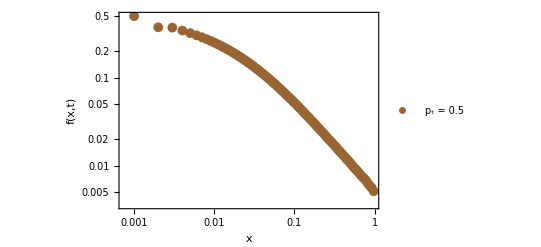

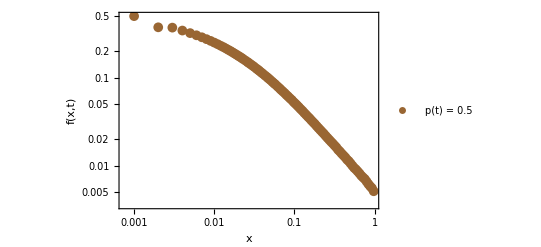

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
theta=4 N1 mu L;
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_pt_5_correct.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s/1000, x11s/1000 1000  x21s/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Orange},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.5"},PlotRange->{{0.001,1},{1,300000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Brown},PlotLegends->{"p_t = 0.5"},PlotRange->All, PlotMarkers->{"●",10}];


(*Show both plots*)
Show[a1sCombined]
```

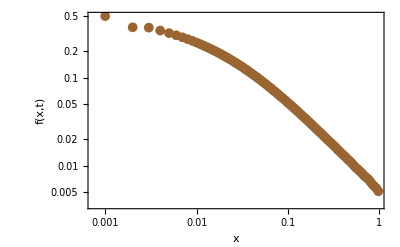
```mathematica
s5=-Graphics-;
```

### Diffusion

```mathematica
Quit[]
```

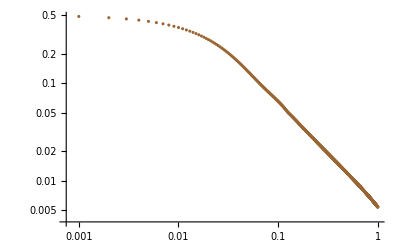

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 h s N1);
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,800}];

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,800},{x,0,1}];
gData=Table[G[x,105.9]/(x*(1-x)),{x,0.001,0.999,0.001}];


xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis ,xaxis  gData/theta};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Brown]
```

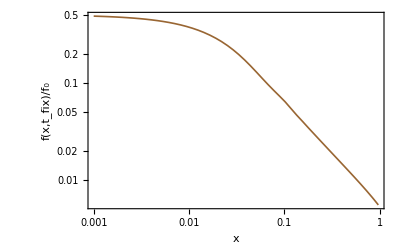

```mathematica
Data1s=Data;

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.0001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];


a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.5"},PlotRange->All, PlotMarkers->{"●",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Brown,Thickness[0.003]}];

(*Show both plots*)
Show[a1sInterpolated]
```

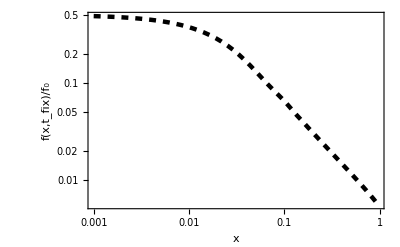
```mathematica
d5=-Graphics-;
```

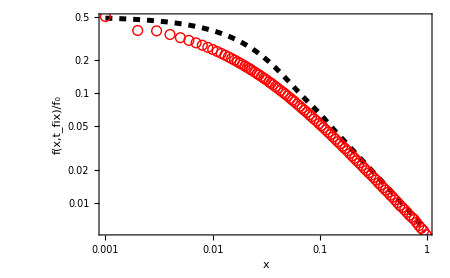

```mathematica
Show[d5,s5]
```

## pt = 0.7

### Simulations

```mathematica
4 N1 mu L
```

400

```mathematica
Quit[]
```

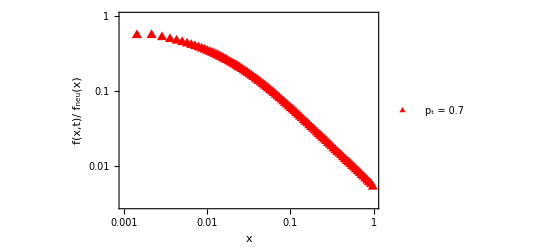

-Graphics-

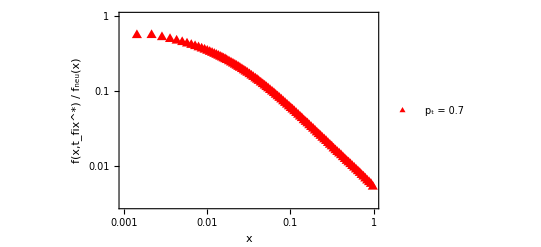

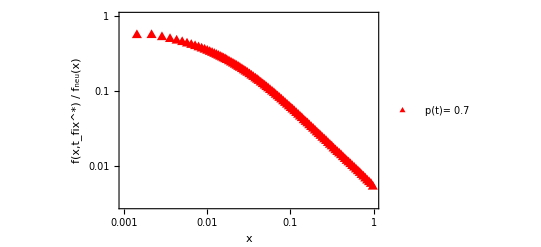

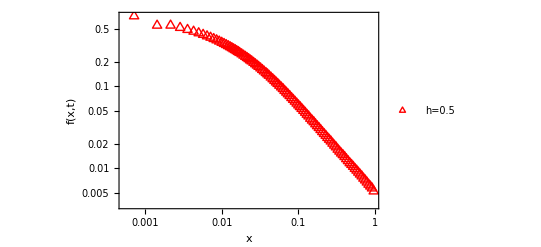

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
theta=4 N1 mu L;
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_pt_7_correct.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s/1400,1400  x11s/1400  x21s/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Orange},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.5"},PlotRange->{{0.001,1},{1,300000}}];


a1sCombined=ListLogLogPlot[{combinedData},Frame->True(*,FrameLabel->{"x","f(x,t_fix)/f_neu"},*),FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[") / ",Italic],SubscriptBox[Style["f",Italic],"StyleBox[\"neu\",FontSlant->\"Italic\"]"]//DisplayForm,Style["(x)",Italic]}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Red},PlotLegends->{"p_t = 0.7"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"▲",12}]; 

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t)/ f_neu(x)"}(*,FrameLabel->{"x","f(x,t)/ f_neu(x)"}*),FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Red},PlotLegends->{"p_t = 0.7"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->{"▲",12}
] 


Show[a1sCombined]
```

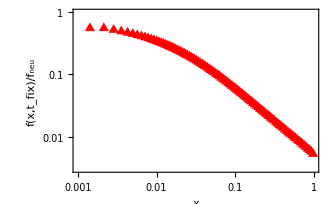
```mathematica
s7=-Graphics-;
```

```mathematica
Quit[]
```

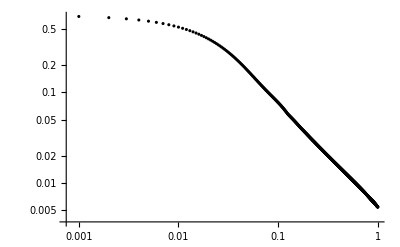

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 h s N1);
x1=NDSolveValue[{D[x2a[t],t]==s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1-2 x2a[t])),x2a[0]==x0},x2a,{t,0,800}];

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,800},{x,0,1}];
gData=Table[G[x,123]/(x*(1-x)),{x,0.001,0.999,0.001}];


xaxis=Table[x,{x,0.001,0.999,0.001}];

Data=Transpose@{xaxis ,xaxis gData/theta};
Data1=Interpolation@Data;

a4=ListLogLogPlot[Data,PlotStyle->Black]
```

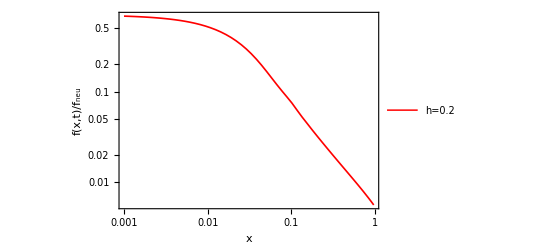

```mathematica
Data1s=Data;

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Orange},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.5"},PlotRange->{{0.001,1},{1,300000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.5"},PlotRange->All, PlotMarkers->{"○",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red,Thickness[0.003]},PlotLegends->{"h=0.2"},PlotRange->All];

(*Show both plots*)
Show[a1sInterpolated]
```

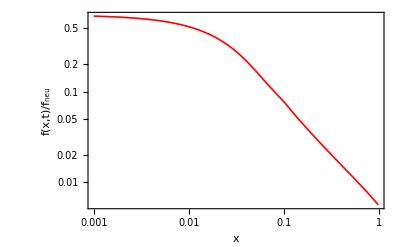
```mathematica
d7=-Graphics-;
```

```mathematica
d5=-Graphics-;
```

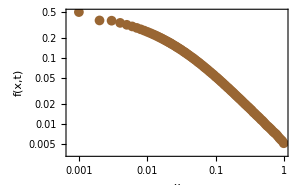
```mathematica
s5=-Graphics-;
```

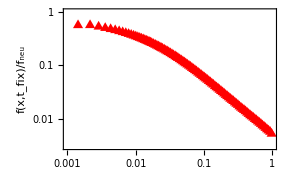
```mathematica
s7=-Graphics-;
```

```mathematica
Show[s7,s5,d7,d5]
```

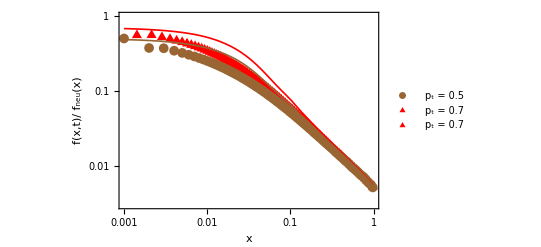

```mathematica
Show[a1sCombined, a1]
```

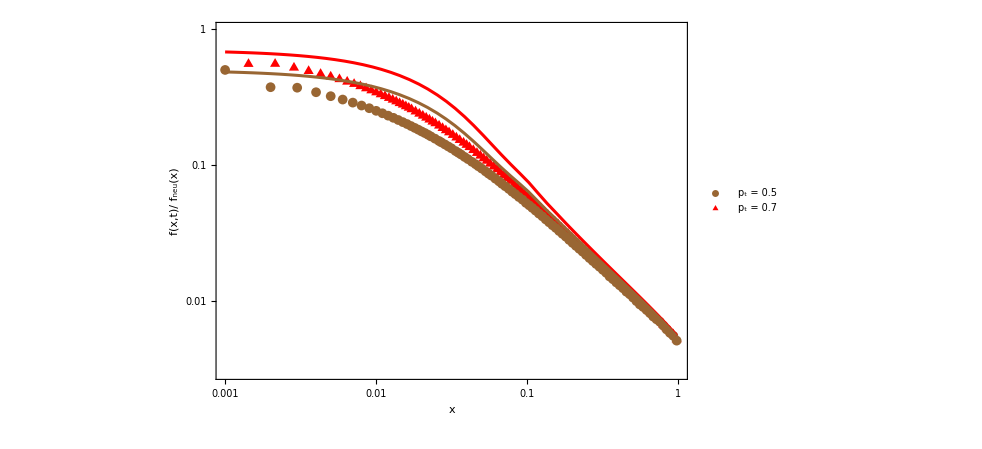

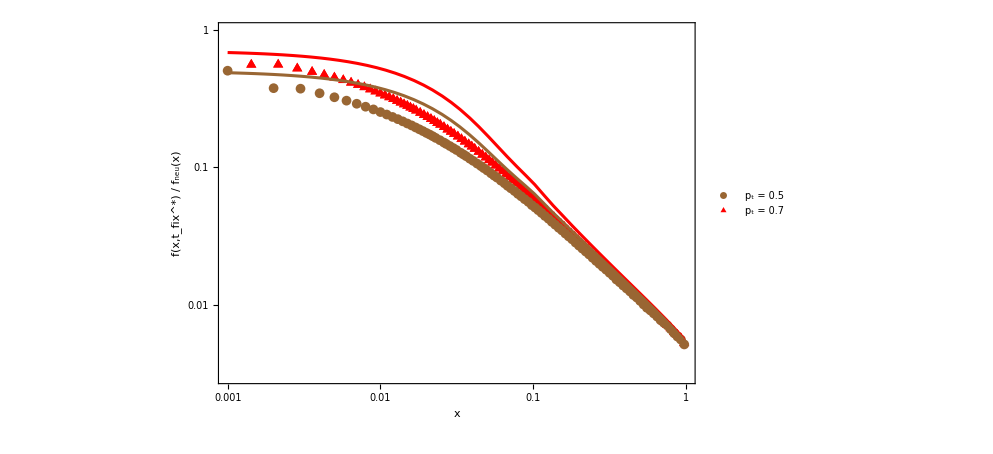

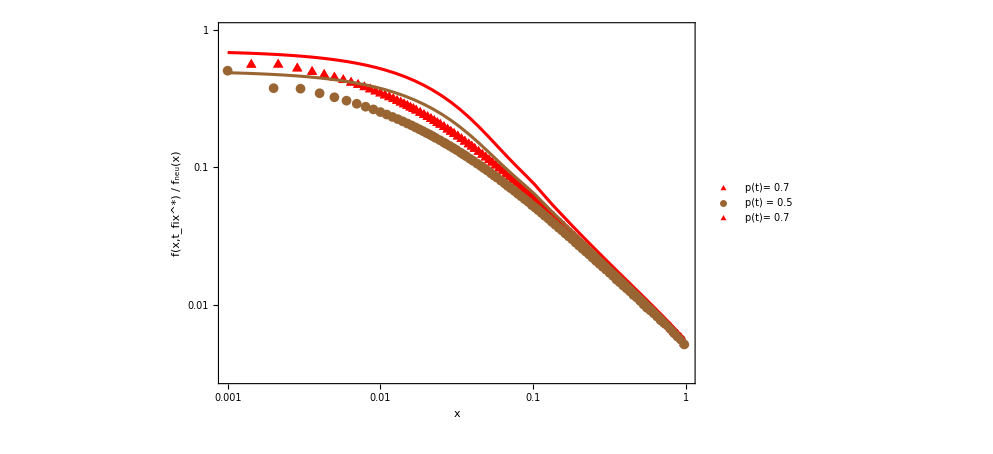

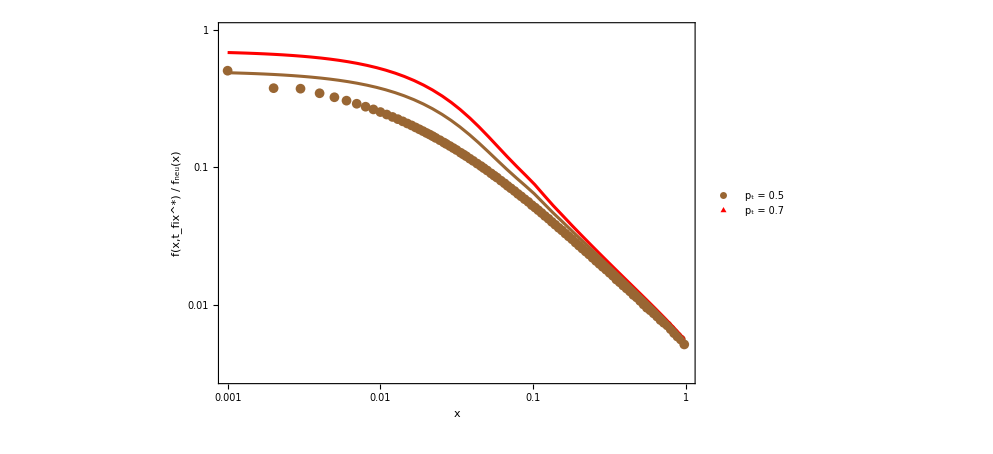
```mathematica
a1=-Graphics-;
```

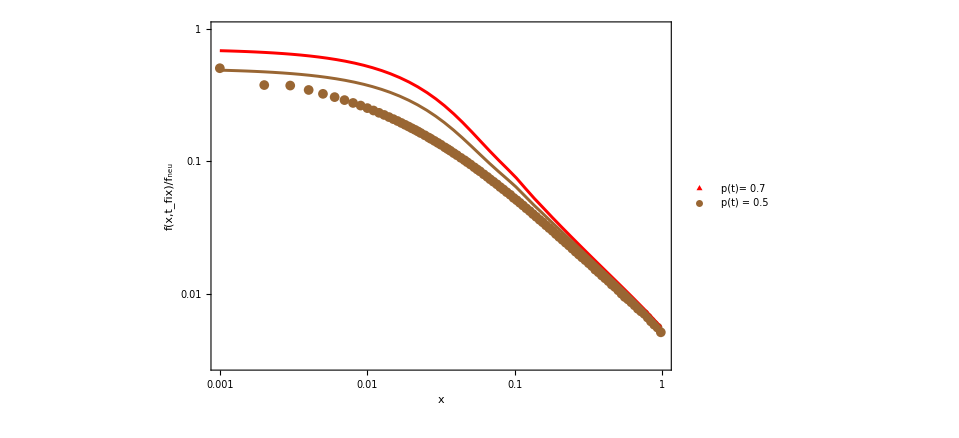
```mathematica
a1=-Graphics-;
```

```mathematica
Show[d7,s7,d5,s5]
```

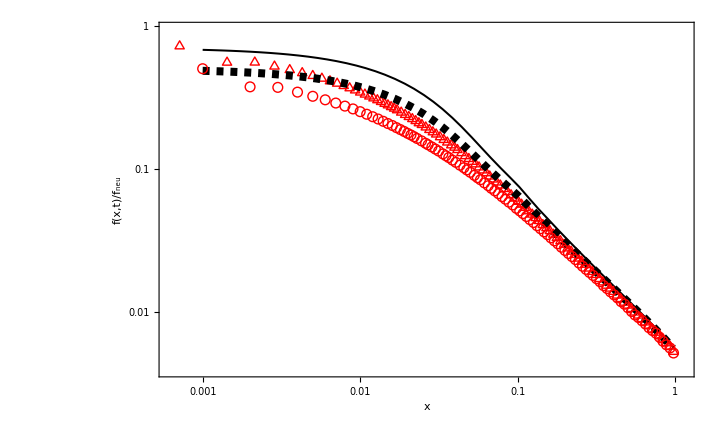

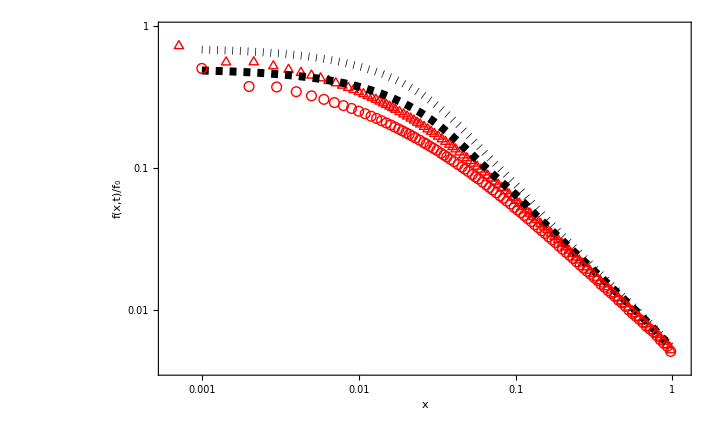

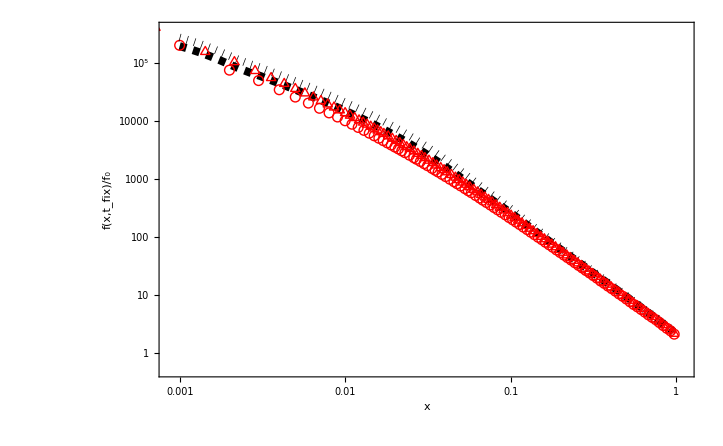

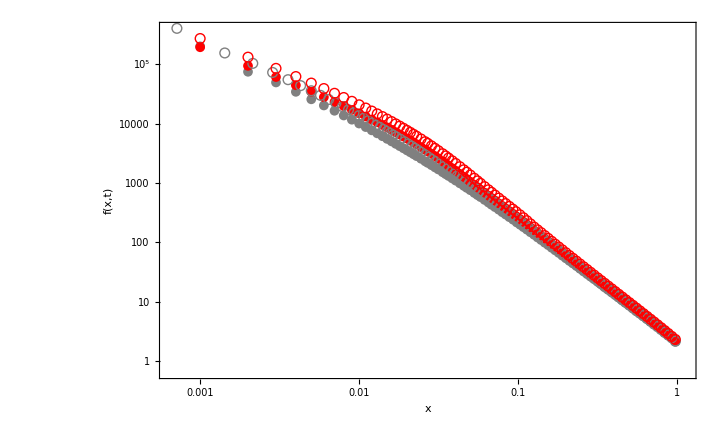

## Inset

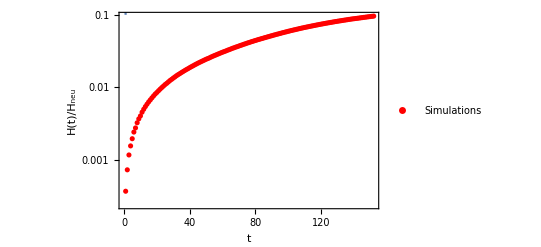

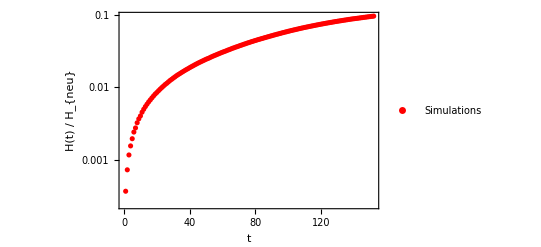

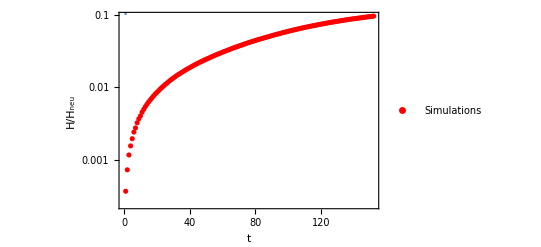

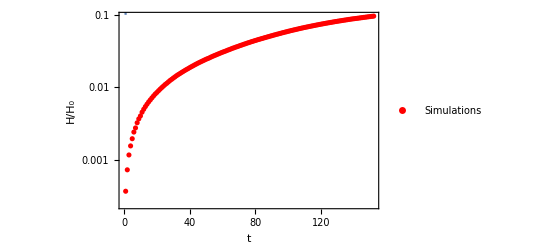

```mathematica
(*e1:25000000,fixevents:2344594.000000,pf:0.093784,tf:0.000000,theta:0.100000,N:500,s:0.050000
*)
s1s=OpenRead["/Users/user/Documents/UNC_work/project_1/C_programs/sub_population/Het/het_t_Ns_25_nt.txt"];

datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];
x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];
theta=0.1;
Data1s=Transpose@{x11s,x21s/theta};
a1s=ListLogPlot[{Data1s}, (*PlotRange->{{0,0.9999},{0,1000}},*) Frame->True, FrameLabel->{"t","H(t)/H_neu"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"Simulations"}];
theta=0.1;

a2s=LogPlot[theta/x,{x,0,1}];

Show[a1s,a2s]
```

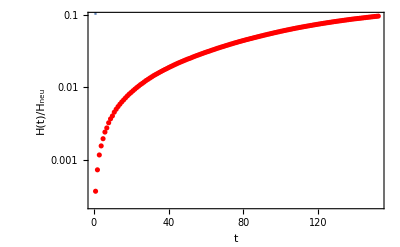
```mathematica
a2=-Graphics-;
```

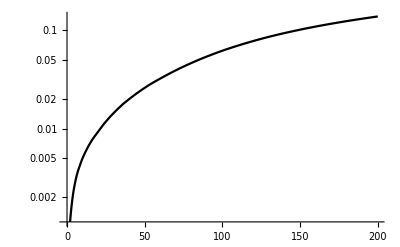
```mathematica
a1=-Graphics-;
```

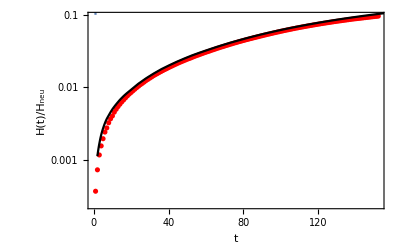

```mathematica
Show[a2,a1]
```

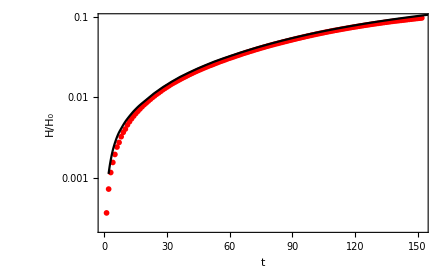

Processing file number: 1

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Processing file number: 2

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Processing file number: 3

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Processing file number: 4

Processing file number: 5

Processing file number: 6

Processing file number: 7

Processing file number: 8

Processing file number: 9

Processing file number: 10

Processing file number: 11

Processing file number: 12

Processing file number: 13

Processing file number: 14

Processing file number: 15

Processing file number: 16

Processing file number: 17

Processing file number: 18

Processing file number: 19

Processing file number: 20

Processing file number: 21

Processing file number: 22

Processing file number: 23

Processing file number: 24

Processing file number: 25

Processing file number: 26

Processing file number: 27

Processing file number: 28

Processing file number: 29

Processing file number: 30

Processing file number: 31

Processing file number: 32

Processing file number: 33

Processing file number: 34

Processing file number: 35

Processing file number: 36

Processing file number: 37

Processing file number: 38

Processing file number: 39

Processing file number: 40

Processing file number: 41

Processing file number: 42

Processing file number: 43

Processing file number: 44

Processing file number: 45

Processing file number: 46

Processing file number: 47

Processing file number: 48

Processing file number: 49

Processing file number: 50

Processing file number: 51

Processing file number: 52

Processing file number: 53

Processing file number: 54

Processing file number: 55

Processing file number: 56

Processing file number: 57

Processing file number: 58

Processing file number: 59

Processing file number: 60

Processing file number: 61

Processing file number: 62

Processing file number: 63

Processing file number: 64

Processing file number: 65

Processing file number: 66

Processing file number: 67

Processing file number: 68

Processing file number: 69

Processing file number: 70

Processing file number: 71

Processing file number: 72

Processing file number: 73

Processing file number: 74

Processing file number: 75

Processing file number: 76

Processing file number: 77

Processing file number: 78

Processing file number: 79

Processing file number: 80

Processing file number: 81

Processing file number: 82

Processing file number: 83

Processing file number: 84

Processing file number: 85

Processing file number: 86

Processing file number: 87

Processing file number: 88

Processing file number: 89

Processing file number: 90

Processing file number: 91

Processing file number: 92

Processing file number: 93

Processing file number: 94

Processing file number: 95

Processing file number: 96

Processing file number: 97

Processing file number: 98

Processing file number: 99

Processing file number: 100

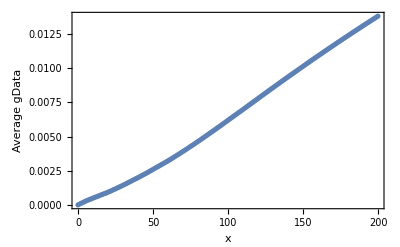

```mathematica
N1=500;
s=0.05;
theta=0.1;
trajDirectory="/Users/user/Documents/UNC_work/project_1/C_programs/sub_population/Ns_25/";
averagehet={};

Do[
Print["Processing file number: ",i];
trajFile=OpenRead[StringJoin[trajDirectory,"traj_",ToString[i],".txt"]];
trajData=ReadList[trajFile,{Number,Number}];
trajInterpolation=Interpolation[trajData];

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(2 N1*trajInterpolation[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==trajInterpolation[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,600},{x,0,1}];

gData=Table[NIntegrate[G[x,tvalue],{x,0.01,0.99}],{tvalue,0,200}];

AppendTo[averagehet,gData];

Close[trajFile];,{i,1,100}];

averageHet=Mean[averagehet];

xaxis=Table[t,{t,0,200,1}];

ListPlot[Transpose[{xaxis,averageHet}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black]]
```

Syntax::sntxf: "FrameLabel->" cannot be followed by "{t,«232»}".

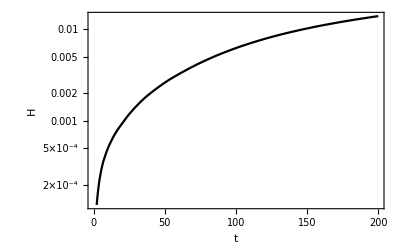

```mathematica
combinedData=Transpose[{xaxis, averageHet}];
interpolation = Interpolation[combinedData];
LogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]}, Frame -> True, FrameLabel -> {"t", "H/H_0"}, FrameStyle -> Directive[Thickness[0.005], Black], PlotStyle -> Black]
```

```mathematica
LogPlot[interpolation[x]/theta,{x,-0.5,Max[combinedData[[All,1]]]} ,PlotStyle -> Black]
```

InterpolatingFunction::dmval: Input value {-0.495904} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## Sample SFS

```mathematica
Quit[]
```

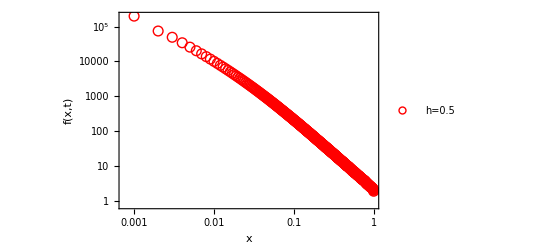

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
theta=4 N1 mu L;
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_pt_5_correct.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1sp5=Transpose@{x11s/1000, 1000  x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=1000;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1sp5,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1sp5,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1sp5},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Orange},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.5"},PlotRange->{{0.001,1},{1,300000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.5"},PlotRange->All, PlotMarkers->{"○",10}];


(*Show both plots*)
Show[a1sCombined]
```

```mathematica
Quit[]
```

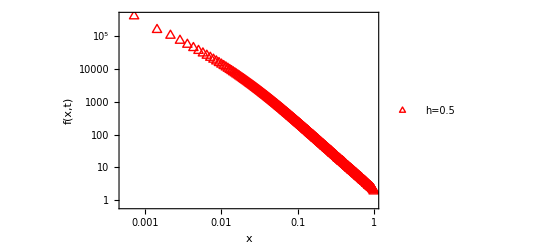

```mathematica
N1=1000;
mu=10^-7;
L=1000000;
theta=4 N1 mu L;
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/time_dependent/Ns_100/t_100/average_data_pt_7_correct.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1sp7=Transpose@{x11s/1400,1400  x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=1000;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1sp7,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1sp7,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1sp7},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Orange},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.5"},PlotRange->{{0.001,1},{1,300000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.5"},PlotRange->All, PlotMarkers->{"△",11}];


(*Show both plots*)
Show[a1sCombined]
```

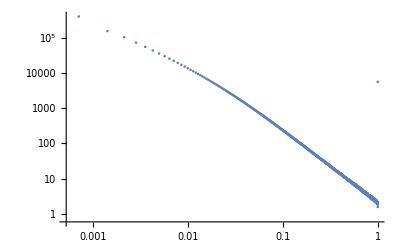

-Graphics-

```mathematica
ListLogLogPlot[Data1sp7, PlotRange->All]
```

```mathematica
a1=-Graphics-;
```

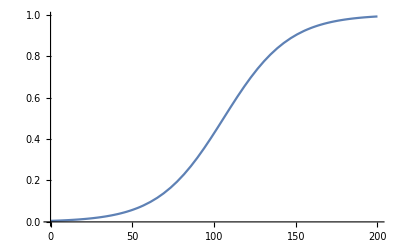

```mathematica
Plot[x1[t],{t,0,200}]
```

```mathematica
x1[123]
```

0.70197

```mathematica
the below is for post fix for which datatfix is in the end
```

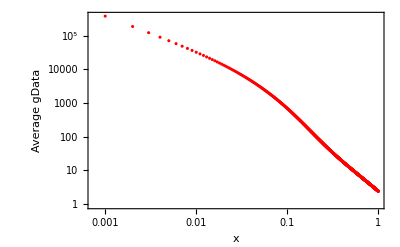

-Graphics-

```mathematica
N1=1000;
mu=10^-7;
L=999999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];



averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[j,2]] G[x,Datatfix[[j,1]]]/(x*(1-x)),{j,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

```mathematica
a2=-Graphics-;
```

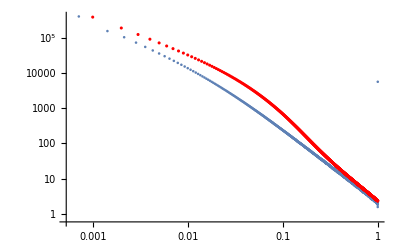

```mathematica
Show[a1,a2]
```

```mathematica
Data1sp99=Transpose@{xaxis,gData};
```

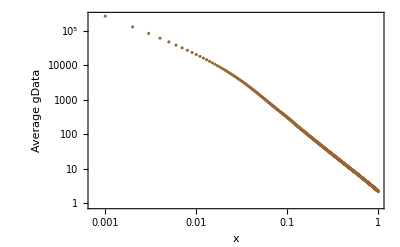

```mathematica
N1=1000;
mu=10^-7;
L=999999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];



averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[ G[x,123]/(x*(1-x)),{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Brown]
```

```mathematica
Data1sp7t=Transpose@{xaxis,gData};
```

```mathematica
Quit[]
```

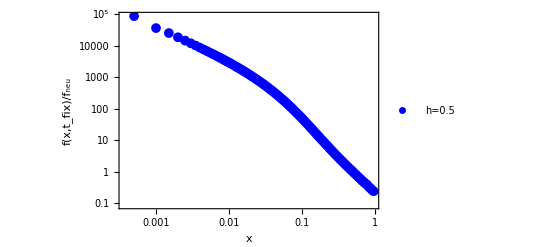

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
(*Read the data*)s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_h_0.5_more_loci.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1sh5=Transpose@{x11s,x21s};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1sh5,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1sh5,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1sh5},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"h=0.5"},PlotRange->All, PlotMarkers->{"●",10}];

(*Show both plots*)
Show[a1sCombined]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

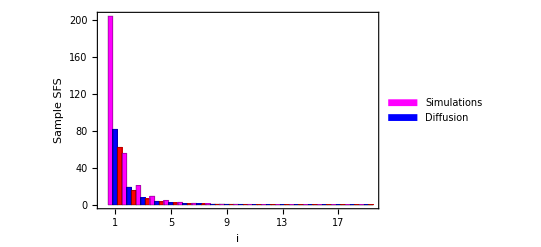

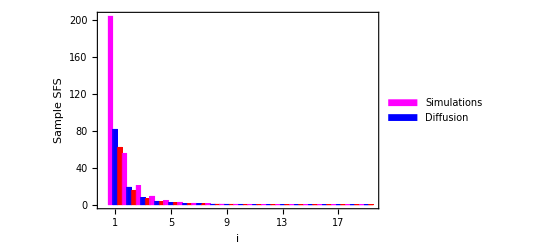

```mathematica
n=20;
N1= 1000;
mu=10^-7;
L=999999;
theta=4N1 mu L;

fun02=Interpolation[Data1sp7]
fun03=Interpolation[Data1sp5]
fun01=Interpolation[Data1sp99]
list01=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun01[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];
list02=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun02[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];
list03=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun03[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];

list6=Table[i,{i,1,n-1,1}];
BarChart[Transpose@{list01,list02, list03},ChartStyle->{ Magenta,Blue, Red},ChartLabels->{{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19", "20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39"},None},Frame->True, FrameLabel->{"i","Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends-> {"Simulations","Diffusion"}](*{Placed[{"c=0.001"},{0.1,0.7}], Placed[{"c=0.01"},{0.5,0.7}] , Placed[{"c=0.1"},{0.5,0.4}] }]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

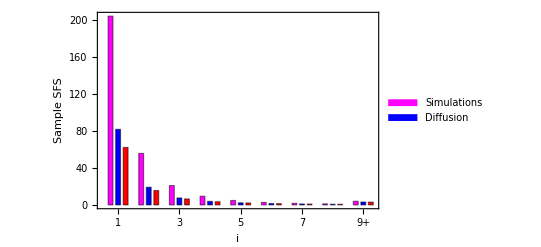

-Graphics-

```mathematica
list01=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun01[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];
list02=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun02[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];
list03=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun03[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];


(*Summing the values from i=9 to n-1 and appending to the lists*)
sumList01=Append[Take[list01,8],Total[Drop[list01,8]]];
sumList02=Append[Take[list02,8],Total[Drop[list02,8]]];
sumList03=Append[Take[list03,8],Total[Drop[list03,8]]];


(*Adjusting the labels to include "9+"*)
labels=Join[Range[1,8],{"9+"}];

BarChart[Transpose@{sumList01,sumList02,sumList03},ChartStyle->{Magenta,Blue,Red},ChartLabels->{labels,None},Frame->True,FrameLabel->{"i","Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"Simulations","Diffusion"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

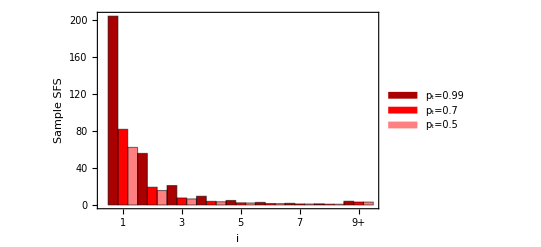

```mathematica
list01=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun01[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];
list02=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun02[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];
list03=Table[n!/((n-i)! i!) NIntegrate[x^i (1-x)^(n-i) fun03[x],{x,0,1},MaxRecursion->30],{i,1,n-1,1}];


(*Summing the values from i=9 to n-1 and appending to the lists*)
sumList01=Append[Take[list01,8],Total[Drop[list01,8]]];
sumList02=Append[Take[list02,8],Total[Drop[list02,8]]];
sumList03=Append[Take[list03,8],Total[Drop[list03,8]]];


(*Adjusting the labels to include "9+"*)
labels=Join[Range[1,8],{"9+"}];

BarChart[Transpose@{sumList01,sumList02,sumList03},ChartStyle->{Darker[Red],Red, Lighter[Red,0.5]},ChartLabels->{{"1","2","3","4","5","6","7","8","9+","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39"},None},Frame->True,FrameLabel->{"i"," Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"p_t=0.99","p_t=0.7", "p_t=0.5"},BarSpacing->0]
```

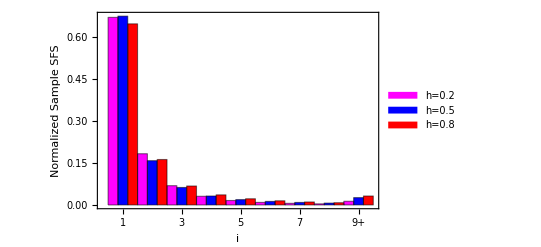

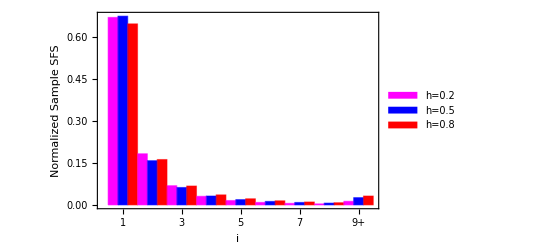

```mathematica
normalizeList[lst_]:=lst/Total[lst]

list01Normalized=normalizeList[sumList01];
list02Normalized=normalizeList[sumList02];
list03Normalized=normalizeList[sumList03];

BarChart[Transpose[{list01Normalized,list02Normalized,list03Normalized}],ChartStyle->{Magenta,Blue,Red},ChartLabels->{labels,None},Frame->True,FrameLabel->{"StyleBox[\"i\",FontSlant->\"Italic\"]","Normalized Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"StyleBox[\"h\",FontSlant->\"Italic\"]StyleBox[\"=\",FontSlant->\"Italic\"]StyleBox[\"0.2\",FontSlant->\"Italic\"]","StyleBox[\"h\",FontSlant->\"Italic\"]StyleBox[\"=\",FontSlant->\"Italic\"]StyleBox[\"0.5\",FontSlant->\"Italic\"]","StyleBox[\"h\",FontSlant->\"Italic\"]StyleBox[\"=\",FontSlant->\"Italic\"]StyleBox[\"0.8\",FontSlant->\"Italic\"]"},BarSpacing->0]
```

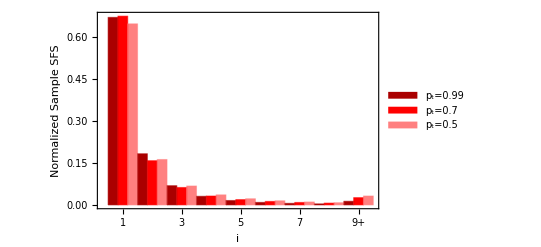

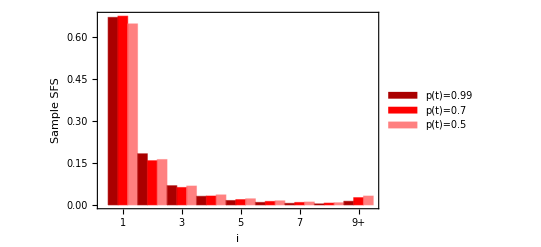

```mathematica
BarChart[Transpose@{list01Normalized,list02Normalized,list03Normalized},ChartStyle->{Darker[Red],Red, Lighter[Red,0.5]},ChartLabels->{{"1","2","3","4","5","6","7","8","9+","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39"},None},Frame->True,FrameLabel->{"i","Normalized Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"p_t=0.99","p_t=0.7", "p_t=0.5"},BarSpacing->0]
```

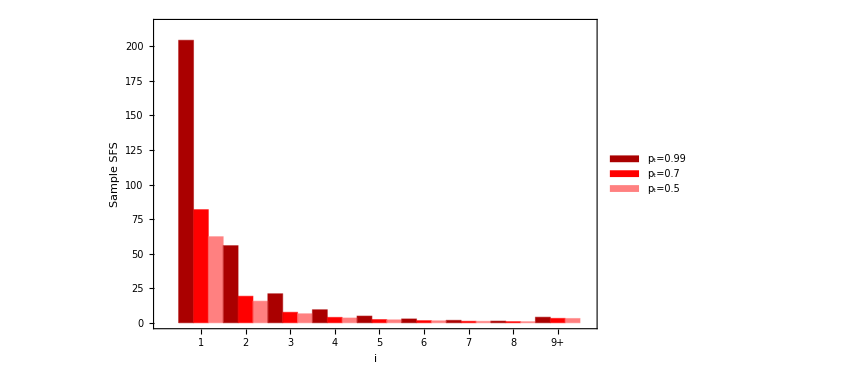

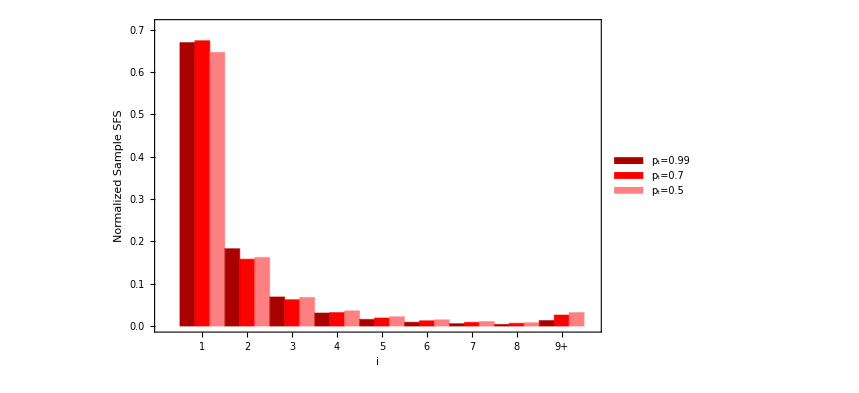

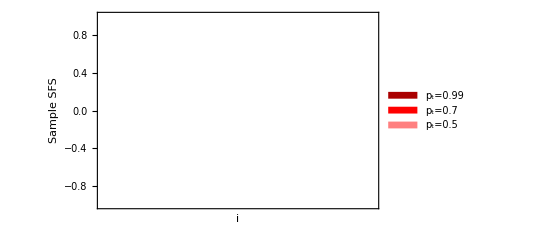

-Graphics-

```mathematica
BarChart[Transpose@{list01Normalized,list02Normalized,list03Normalized},ChartStyle->{Darker[Red],Red, Lighter[Red,0.5]},ChartLabels->{{"1","2","3","4","5","6","7","8","9+","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39"},None},Frame->True,FrameLabel->{"i","Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"p_t=0.99","p_t=0.7", "p_t=0.5"},BarSpacing->0]
```

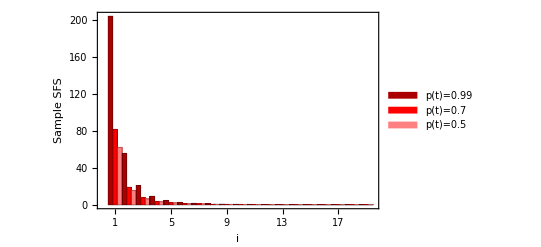

```mathematica
BarChart[Transpose@{list01,list02,list03},ChartStyle->{Darker[Red],Red, Lighter[Red,0.5]},ChartLabels->{{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39"},None},Frame->True,FrameLabel->{"i","Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends->{"p(t)=0.99","p(t)=0.7", "p(t)=0.5"}]
```

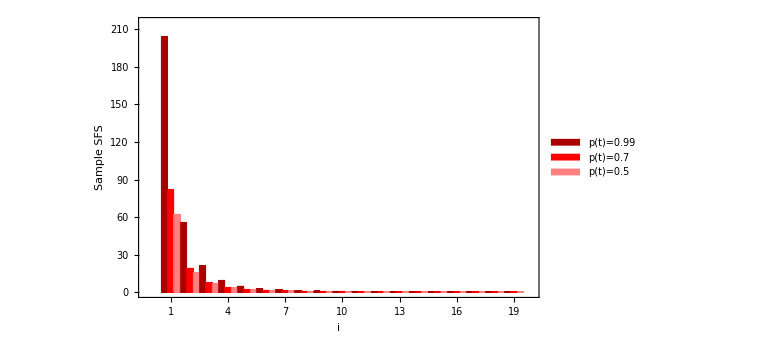

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

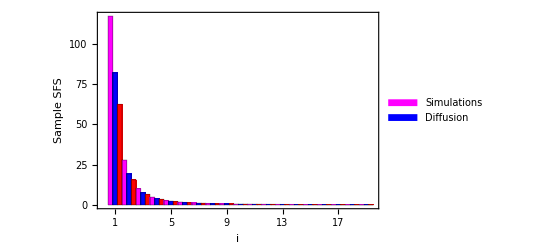

```mathematica
n=20;
N1= 1000;
mu=10^-7;
L=999999;
theta=4N1 mu L;

fun02=Interpolation[Data1sp7]
fun03=Interpolation[Data1sp5]
fun01=Interpolation[Data1sp7t]
list01=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun01[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];
list02=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun02[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];
list03=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun03[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];

list6=Table[i,{i,1,n-1,1}];
BarChart[Transpose@{list01,list02, list03},ChartStyle->{ Magenta,Blue, Red},ChartLabels->{{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19", "20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39"},None},Frame->True, FrameLabel->{"i","Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium],BaseStyle->{FontWeight->"Bold",FontSize->10,FontFamily->"Calibri"},ChartLegends-> {"Simulations","Diffusion"}](*{Placed[{"c=0.001"},{0.1,0.7}], Placed[{"c=0.01"},{0.5,0.7}] , Placed[{"c=0.1"},{0.5,0.4}] }]*)
```

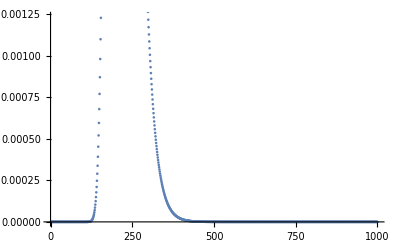

```mathematica
ListPlot[Datatfix]
```

### Datatfix

```mathematica
Datatfix={{1,0.},{2,0.},{3,4.151047251472476*^-295},{4,4.1989426350820763*^-252},{5,1.941016690045759*^-222},{6,2.608276309898929*^-200},{7,6.179003509137429*^-183},{8,8.628412609395431*^-169},{9,5.835201420580849*^-157},{10,7.381361825898198*^-147},{11,4.34982745842995*^-138},{12,2.2685953183050454*^-130},{13,1.6693189929204664*^-123},{14,2.455247572800332*^-117},{15,9.41964387451671*^-112},{16,1.160006854315179*^-106},{17,5.4050572873193316*^-102},{18,1.0877283612689127*^-97},{19,1.0530859161798492*^-93},{20,5.361157670900453*^-90},{21,1.545578009678681*^-86},{22,2.6855336367126233*^-83},{23,2.9650850710835503*^-80},{24,2.1763768897952057*^-77},{25,1.1041079593334904*^-74},{26,4.0040616035294655*^-72},{27,1.0689356054105126*^-69},{28,2.1554363856823506*^-67},{29,3.358070300673084*^-65},{30,4.1240145846763665*^-63},{31,4.06408513811136*^-61},{32,3.265288701530391*^-59},{33,2.169609722662746*^-57},{34,1.2075471499563959*^-55},{35,5.695167111170505*^-54},{36,2.300013037798592*^-52},{37,8.029694068621752*^-51},{38,2.444371809873805*^-49},{39,6.539785272992895*^-48},{40,1.5489105839715121*^-46},{41,3.269162447132942*^-45},{42,6.186487317501928*^-44},{43,1.055584319963514*^-42},{44,1.6324547956672707*^-41},{45,2.2992175785884245*^-40},{46,2.9624438473054035*^-39},{47,3.5063509239106313*^-38},{48,3.8271558064045856*^-37},{49,3.866164028549318*^-36},{50,3.626880146769935*^-35},{51,3.1696176363056452*^-34},{52,2.5881399328855507*^-33},{53,1.9800857448663394*^-32},{54,1.4230884357957956*^-31},{55,9.631670940860237*^-31},{56,6.1532220496451005*^-30},{57,3.71867270076802*^-29},{58,2.1303898529866206*^-28},{59,1.1592292258659857*^-27},{60,6.0024358686058696*^-27},{61,2.962792797068715*^-26},{62,1.3964319439816775*^-25},{63,6.294721089584316*^-25},{64,2.717888382807554*^-24},{65,1.1256782266227035*^-23},{66,4.478416851509304*^-23},{67,1.7137018831624165*^-22},{68,6.315300147878256*^-22},{69,2.2440072735559535*^-21},{70,7.69710166416402*^-21},{71,2.5514258945071954*^-20},{72,8.18185352299972*^-20},{73,2.540826321195483*^-19},{74,7.648507396566395*^-19},{75,2.2339017561236765*^-18},{76,6.336196011097267*^-18},{77,1.746814864980432*^-17},{78,4.684695490987933*^-17},{79,1.2231540365352046*^-16},{80,3.1115918235205906*^-16},{81,7.718094467615425*^-16},{82,1.8679979768425794*^-15},{83,4.414519923852513*^-15},{84,1.019348889008096*^-14},{85,2.301315327720187*^-14},{86,5.08294559418484*^-14},{87,1.0990158784361496*^-13},{88,2.3275345518857856*^-13},{89,4.831012992839563*^-13},{90,9.832603122724718*^-13},{91,1.9634408466396947*^-12},{92,3.848661030617397*^-12},{93,7.40901717071295*^-12},{94,1.4014594447602657*^-11},{95,2.605991244202105*^-11},{96,4.765793128315711*^-11},{97,8.575484224870336*^-11},{98,1.518899604915662*^-10},{99,2.649272774987421*^-10},{100,4.5522534720939185*^-10},{101,7.709003141338209*^-10},{102,1.2870843501179057*^-9},{103,2.119400540646493*^-9},{104,3.443277277345807*^-9},{105,5.5212212713639226*^-9},{106,8.740766706930477*^-9},{107,1.366652296482317*^-8},{108,2.1110552881173496*^-8},{109,3.222621780221304*^-8},{110,4.863160491412253*^-8},{111,7.256967501258395*^-8},{112,1.071132906910046*^-7},{113,1.5642424813441047*^-7},{114,2.2607626951384421*^-7},{115,3.234525351464234*^-7},{116,4.5822865384976217*^-7},{117,6.429518904135728*^-7},{118,8.937268949845144*^-7},{119,1.231017021205386*^-6},{120,1.6805685021735479*^-6},{121,2.274462220215032*^-6},{122,3.0522945299676313*^-6},{123,4.062484580425064*^-6},{124,5.363700873910105*^-6},{125,7.026394485742704*^-6},{126,9.134420576502699*^-6},{127,0.000011786723729324329},{128,0.000015099056446895347},{129,0.000019205694084524976},{130,0.000024261103839283106},{131,0.000030441520413983366},{132,0.000037946376975868137},{133,0.00004699953707811196},{134,0.00005785027189654513},{135,0.00007077392720233829},{136,0.00008607222643895225},{137,0.00010407315995607785},{138,0.00012513041597996682},{139,0.0001496223161245764},{140,0.00017795022714563223},{141,0.00021053643086990718},{142,0.0002478214456620386},{143,0.0002902608050241965},{144,0.000338321311654779},{145,0.0003924767980889451},{146,0.0004532034379314917},{147,0.0005209746624879418},{148,0.0005962557507400034},{149,0.0006794981673719203},{150,0.0007711337337234204},{151,0.0008715687188915334},{152,0.000981177960673044},{153,0.0011002990764081867},{154,0.0012292269047438158},{155,0.0013682082390137945},{156,0.0015174369565959832},{157,0.0016770496199630873},{158,0.0018471216288104624},{159,0.002027663985535426},{160,0.002218620729212662},{161,0.002419867080444667},{162,0.0026312083272395886},{163,0.002852379469391826},{164,0.0030830456261394515},{165,0.003322803199431707},{166,0.003571181773220509},{167,0.0038276467180271556},{168,0.004091602459830286},{169,0.004362396363240731},{170,0.004639323171102359},{171,0.004921629936176424},{172,0.005208521375485127},{173,0.005499165574226702},{174,0.005792699963914699},{175,0.006088237498494226},{176,0.006384872952577875},{177,0.006681689267529671},{178,0.0069777638737983155},{179,0.00727217492153483},{180,0.007564007355992076},{181,0.007852358779354937},{182,0.008136345046348838},{183,0.008415105547080958},{184,0.00868780813694933},{185,0.008953653679979297},{186,0.009211880178497426},{187,0.009461766468521095},{188,0.009702635466561893},{189,0.00993385695942514},{190,0.010154849934198684},{191,0.010365084452580763},{192,0.010564083073826318},{193,0.010751421841922197},{194,0.010926730850363466},{195,0.011089694404538454},{196,0.01124005080362},{197,0.011377591766348033},{198,0.011502161526960982},{199,0.011613655628935347},{200,0.011712019445153165},{201,0.011797246453661807},{202,0.011869376298355064},{203,0.011928492663723663},{204,0.0119747209923322},{205,0.012008226072916134},{206,0.012029209525994728},{207,0.012037907212697109},{208,0.012034586591136851},{209,0.012019544043178235},{210,0.011993102192843719},{211,0.011955607235951031},{212,0.011907426298861786},{213,0.011848944842498408},{214,0.011780564126065646},{215,0.011702698743212345},{216,0.011615774241708517},{217,0.011520224836106136},{218,0.011416491221308828},{219,0.011305018493508992},{220,0.01118625418356652},{221,0.01106064640660665},{222,0.010928642130411568},{223,0.010790685564071263},{224,0.01064721666734632},{225,0.010498669780278717},{226,0.010345472371764395},{227,0.010188043905070767},{228,0.010026794817642754},{229,0.009862125611984513},{230,0.00969442605393122},{231,0.009524074474228884},{232,0.009351437169015852},{233,0.009176867894543297},{234,0.009000707451277333},{235,0.00882328336792936},{236,0.00864490960272108},{237,0.008465886364881822},{238,0.00828650016208229},{239,0.008107023521385193},{240,0.00792771514364187},{241,0.0077488199404423625},{242,0.007570569151566309},{243,0.007393180507127953},{244,0.00721685842995449},{245,0.007041794273915279},{246,0.006868166594109086},{247,0.006696141445015374},{248,0.006525872702918019},{249,0.006357502409117392},{250,0.0061911611306176275},{251,0.006026968335484171},{252,0.005865032779225927},{253,0.005705452900856585},{254,0.005548317224869259},{255,0.00539370476764898},{256,0.005241685445986877},{257,0.0050923204858414305},{258,0.0049456628296292915},{259,0.004801757540495436},{260,0.004660642202172029},{261,0.00452234731318627},{262,0.0043868966743194245},{263,0.004254307768352964},{264,0.004124592131263798},{265,0.003997755714148117},{266,0.003873799235264416},{267,0.003752718521688727},{268,0.003634504840169495},{269,0.0035191452168563788},{270,0.003406622745656299},{271,0.0032969168850424816},{272,0.0031900037432092574},{273,0.003085856351526168},{274,0.0029844449263004727},{275,0.002885737118906698},{276,0.002789698254385127},{277,0.002696291558649337},{278,0.0026054783744761745},{279,0.0025172183664811322},{280,0.0024314697153086443},{281,0.002348189301293944},{282,0.0022673328778428994},{283,0.00218885523493054},{284,0.002112710352627017},{285,0.0020388515459066623},{286,0.001967231599587107},{287,0.001897802895157967},{288,0.0018305175289654151},{289,0.001765327422368828},{290,0.0017021844241580635},{291,0.0016410404055571877},{292,0.0015818473481477124},{293,0.0015245574250361078},{294,0.0014691230755424357},{295,0.00141549707372549},{296,0.0013636325911792753},{297,0.0013134832541589565},{298,0.001265003195530051},{299,0.0012181471016771172},{300,0.0011728702548595682},{301,0.0011291285709811502},{302,0.0010868786332728485},{303,0.0010460777219550791},{304,0.0010066838403821482},{305,0.0009686557375555817},{306,0.0009319529273852454},{307,0.0008965357050926071},{308,0.000862365160613139},{309,0.0008294031894303066},{310,0.0007976125009428514},{311,0.0007669566245632534},{312,0.0007373999136319462},{313,0.0007089075475754059},{314,0.0006814455319584896},{315,0.000654980697151983},{316,0.0006294806953267062},{317,0.0006049139960954925},{318,0.00058124988087452},{319,0.000558458436083978},{320,0.000536510545305963},{321,0.0005153778804307962},{322,0.0004950328920984825},{323,0.00047544879917300566},{324,0.0004565995776856349},{325,0.000438459949114869},{326,0.00042100536814718706},{327,0.0004042120099774454},{328,0.0003880567572132102},{329,0.00037251718645658417},{330,0.00035757155452360916},{331,0.00034319878463981326},{332,0.00032937845218182303},{333,0.00031609077048745286},{334,0.0003033165764886098},{335,0.0002910373162999552},{336,0.00027923503078526216},{337,0.0002678923411325874},{338,0.0002569924344690554},{339,0.00024651904953490336},{340,0.000236456462459064},{341,0.0002267894726352495},{342,0.00021750338873814432},{343,0.00020858401486737913},{344,0.00020001763689732202},{345,0.0001917910089707669},{346,0.00018389134020187128},{347,0.00017630628162126568},{348,0.00016902391309147488},{349,0.00016203273105530253},{350,0.0001553216357011953},{351,0.00014887991897525476},{352,0.00014269725259109337},{353,0.0001367636763264836},{354,0.00013106958656949216},{355,0.00012560572511664722},{356,0.00012036316827926292},{357,0.000115333315918589},{358,0.00011050788155148306},{359,0.0001058788816243615},{360,0.00010143862585684659},{361,0.00009717970751268581},{362,0.00009309499397674108},{363,0.00008917761758169334},{364,0.00008542096668208817},{365,0.00008181867697301764},{366,0.00007836462310972465},{367,0.00007505291020990498},{368,0.00007187786648019043},{369,0.00006883403488814214},{370,0.00006591616595088865},{371,0.00006311921039147883},{372,0.000060438312073652706},{373,0.00005786880115163073},{374,0.00005540618743052192},{375,0.00005304615393295302},{376,0.00005078455072792639},{377,0.00004861738859402395},{378,0.00004654083378254239},{379,0.00004455120175912804},{380,0.00004264495203622741},{381,0.00004081868282167731},{382,0.000039069125902269324},{383,0.00003739314169729384},{384,0.0000357877144775829},{385,0.00003424994774560794},{386,0.00003277705977223623},{387,0.000031366379285800606},{388,0.00003001534130919075},{389,0.00002872148314073707},{390,0.000027482440474722996},{391,0.00002629594365742652},{392,0.000025159814074666507},{393,0.000024071960666898696},{394,0.0000230303765679855},{395,0.000022033135863838823},{396,0.000021078390467213606},{397,0.000020164367155095347},{398,0.00001928936441453749},{399,0.000018451750145217068},{400,0.00001764995846239918},{401,0.000016882487349907102},{402,0.00001614789610811625},{403,0.0000154448029444047},{404,0.000014771882652904125},{405,0.000014127864380563488},{406,0.000013511529476556649},{407,0.000012921709422561713},{408,0.000012357283840242284},{409,0.000011817178574513765},{410,0.000011300363849028592},{411,0.000010805852491754474},{412,0.000010332698228166285},{413,9.87999403945038*^-6},{414,9.44687058398223*^-6},{415,9.032494679091803*^-6},{416,8.636067841511751*^-6},{417,8.256824884186519*^-6},{418,7.8940325674471*^-6},{419,7.546988323468246*^-6},{420,7.215018905908449*^-6},{421,6.897479401472125*^-6},{422,6.593751870638248*^-6},{423,6.30324434680196*^-6},{424,6.025389753577599*^-6},{425,5.759644884844954*^-6},{426,5.505489425094661*^-6},{427,5.262425008566899*^-6},{428,5.029974315728443*^-6},{429,4.807680205682334*^-6},{430,4.595104883154085*^-6},{431,4.391829098743771*^-6},{432,4.197451381180414*^-6},{433,4.0115873003579705*^-6},{434,3.8338687599764195*^-6},{435,3.6639433186521116*^-6},{436,3.5014735384026746*^-6},{437,3.3461363594505117*^-6},{438,3.1976225003267336*^-6},{439,3.055635882294744*^-6},{440,2.9198930771473604*^-6},{441,2.790122777466563*^-6},{442,2.6660652884678862*^-6},{443,2.547472040583766*^-6},{444,2.434105121971363*^-6},{445,2.3257368301605644*^-6},{446,2.2221492420868344*^-6},{447,2.1231338017820034*^-6},{448,2.028490925022943*^-6},{449,1.9380296202694494*^-6},{450,1.8515671252106199*^-6},{451,1.7689285583835843*^-6},{452,1.689946585168722*^-6},{453,1.6144610975495238*^-6},{454,1.542318907310977*^-6},{455,1.4733734518495722*^-6},{456,1.4074845122718076*^-6},{457,1.344517943222595*^-6},{458,1.284345413978367*^-6},{459,1.2268441603485548*^-6},{460,1.1718967469469661*^-6},{461,1.1193908394116893*^-6},{462,1.0692189861684409*^-6},{463,1.0212784093483374*^-6},{464,9.75470804486162*^-7},{465,9.317021486399053*^-7},{466,8.898825165866181*^-7},{467,8.499259047631254*^-7},{468,8.117500626333183*^-7},{469,7.752763311764253*^-7},{470,7.4042948820271*^-7},{471,7.071376002148176*^-7},{472,6.753318805441872*^-7},{473,6.449465535027795*^-7},{474,6.159187243008177*^-7},{475,5.881882544912068*^-7},{476,5.616976427109766*^-7},{477,5.36391910499307*^-7},{478,5.12218492980645*^-7},{479,4.891271342098901*^-7},{480,4.670697869849566*^-7},{481,4.4600051693984824*^-7},{482,4.258754107390246*^-7},{483,4.066524882011548*^-7},{484,3.882916181873073*^-7},{485,3.7075443809544506*^-7},{486,3.540042768094926*^-7},{487,3.380060809574803*^-7},{488,3.2272634433928133*^-7},{489,3.0813304039016917*^-7},{490,2.941955575519279*^-7},{491,2.808846374285746*^-7},{492,2.681723156087908*^-7},{493,2.5603186504203055*^-7},{494,2.4443772672022104*^-7},{495,2.33365533539513*^-7},{496,2.2279190930762896*^-7},{497,2.1269457269298918*^-7},{498,2.0305221613372975*^-7},{499,1.9384447754910923*^-7},{500,1.850518988007454*^-7},{501,1.7665588595212625*^-7},{502,1.686386712562737*^-7},{503,1.6098327679513378*^-7},{504,1.53673479700146*^-7},{505,1.4669377876135447*^-7},{506,1.4002936304894208*^-7},{507,1.3366608090138914*^-7},{508,1.2759041117101857*^-7},{509,1.2178943531204902*^-7},{510,1.1625081076303888*^-7},{511,1.1096274549230861*^-7},{512,1.0591397365621863*^-7},{513,1.0109373232231114*^-7},{514,9.649173921133565*^-8},{515,9.209817141413801*^-8},{516,8.790364504465153*^-8},{517,8.389919575229742*^-8},{518,8.007626021174492*^-8},{519,7.642665813872084*^-8},{520,7.294257565203029*^-8},{521,6.961654846989765*^-8},{522,6.644144687092994*^-8},{523,6.34104605838822*^-8},{524,6.051708463242646*^-8},{525,5.775510575501583*^-8},{526,5.511858942320449*^-8},{527,5.260186743235675*^-8},{528,5.01995260397942*^-8},{529,4.7906394626498885*^-8},{530,4.5717534859514285*^-8},{531,4.362823033316671*^-8},{532,4.163397666817939*^-8},{533,3.973047204865802*^-8},{534,3.791360817778741*^-8},{535,3.617946163391747*^-8},{536,3.45242856094934*^-8},{537,3.2944502016046035*^-8},{538,3.1436693939184676*^-8},{539,2.9997598428219345*^-8},{540,2.862409960572575*^-8},{541,2.7313222082992664*^-8},{542,2.606212466791091*^-8},{543,2.486809435244643*^-8},{544,2.372854056739115*^-8},{545,2.2640989692621482*^-8},{546,2.1603079811603253*^-8},{547,2.0612555699371468*^-8},{548,1.9667264033686588*^-8},{549,1.876514881952895*^-8},{550,1.790424701750411*^-8},{551,1.7082684367169764*^-8},{552,1.629867139666152*^-8},{553,1.5550499610353787*^-8},{554,1.483653784685607*^-8},{555,1.4155228799319877*^-8},{556,1.3505085691501202*^-8},{557,1.2884689102373674*^-8},{558,1.2292683932475038*^-8},{559,1.1727776506162912*^-8},{560,1.1188731803453887*^-8},{561,1.0674370815785259*^-8},{562,1.0183568020182545*^-8},{563,9.715248966568506*^-9},{564,9.268387973185644*^-9},{565,8.842005925325997*^-9},{566,8.43516817277666*^-9},{567,8.04698252159067*^-9},{568,7.676597315985789*^-9},{569,7.32319960635471*^-9},{570,6.9860133995478215*^-9},{571,6.664297987757205*^-9},{572,6.357346352496087*^-9},{573,6.064483640323751*^-9},{574,5.785065707116967*^-9},{575,5.518477727833299*^-9},{576,5.264132868798071*^-9},{577,5.021471019898318*^-9},{578,4.78995758367819*^-9},{579,4.569082319086773*^-9},{580,4.358358237302776*^-9},{581,4.157320547310083*^-9},{582,3.965525649103484*^-9},{583,3.7825501721565195*^-9},{584,3.6079900573670327*^-9},{585,3.4414596804164805*^-9},{586,3.2825910147064084*^-9},{587,3.1310328320946365*^-9},{588,2.986449939733223*^-9},{589,2.8485224515497435*^-9},{590,2.7169450918764634*^-9},{591,2.5914265318231673*^-9},{592,2.4716887553270905*^-9},{593,2.357466452485664*^-9},{594,2.248506442208902*^-9},{595,2.1445671200482145*^-9},{596,2.045417931209196*^-9},{597,1.950838867429295*^-9},{598,1.8606199866458609*^-9},{599,1.7745609544290112*^-9},{600,1.6924690790733423*^-9},{601,1.6141665293035657*^-9},{602,1.5394746640290606*^-9},{603,1.4682289227431647*^-9},{604,1.4002708262980956*^-9},{605,1.335449156944735*^-9},{606,1.2736196270013268*^-9},{607,1.214644562566819*^-9},{608,1.1583926016004472*^-9},{609,1.1047384057341762*^-9},{610,1.053562385078251*^-9},{611,1.0047504358665811*^-9},{612,9.581936894956294*^-10},{613,9.13788273426933*^-10},{614,8.714350829551594*^-10},{615,8.310395630139224*^-10},{616,7.925114999358071*^-10},{617,7.55764823575386*^-10},{618,7.207174170106092*^-10},{619,6.872909360260695*^-10},{620,6.554106363310525*^-10},{621,6.250052088401325*^-10},{622,5.960066222866152*^-10},{623,5.683499732008539*^-10},{624,5.419733426000772*^-10},{625,5.168176592612663*^-10},{626,4.928265692388234*^-10},{627,4.699463112609127*^-10},{628,4.48125597964842*^-10},{629,4.273155024158893*^-10},{630,4.074693498686988*^-10},{631,3.885426144759145*^-10},{632,3.704928206432845*^-10},{633,3.5327944904106727*^-10},{634,3.3686384677169346*^-10},{635,3.21209141687161*^-10},{636,3.062801606501471*^-10},{637,2.9204335147235527*^-10},{638,2.784667085494839*^-10},{639,2.655197017316296*^-10},{640,2.5317320858294536*^-10},{641,2.413994496244102*^-10},{642,2.3017192672182888*^-10},{643,2.1946536407026967*^-10},{644,2.0925565204552712*^-10},{645,1.9951979356396655*^-10},{646,1.902358529104644*^-10},{647,1.8138290691146487*^-10},{648,1.7294099834659472*^-10},{649,1.648910914937274*^-10},{650,1.5721502972726861*^-10},{651,1.4989549500351928*^-10},{652,1.4291596931890943*^-10},{653,1.3626069782528685*^-10},{654,1.2991465367387653*^-10},{655,1.2386350449607175*^-10},{656,1.1809358040050925*^-10},{657,1.1259184344497395*^-10},{658,1.0734585851026396*^-10},{659,1.0234376551179621*^-10},{660,9.757425288781992*^-11},{661,9.302653230548487*^-11},{662,8.869031452951925*^-11},{663,8.455578639888967*^-11},{664,8.061358886089865*^-11},{665,7.685479603304168*^-11},{666,7.327089519795208*^-11},{667,6.985376773718016*^-11},{668,6.659567093959975*^-11},{669,6.34892206523653*^-11},{670,6.052737469251567*^-11},{671,5.7703417098099175*^-11},{672,5.501094304388394*^-11},{673,5.244384444686074*^-11},{674,4.9996296276039375*^-11},{675,4.7662743466476383*^-11},{676,4.543788844171568*^-11},{677,4.331667921116888*^-11},{678,4.1294298016040486*^-11},{679,3.936615050474461*^-11},{680,3.752785537538918*^-11},{681,3.5775234558926166*^-11},{682,3.410430380368191*^-11},{683,3.2511263692386496*^-11},{684,3.099249110618103*^-11},{685,2.9544531061049174*^-11},{686,2.8164088925673565*^-11},{687,2.684802299834962*^-11},{688,2.5593337426564162*^-11},{689,2.4397175458520536*^-11},{690,2.325681297608396*^-11},{691,2.2169652401252548*^-11},{692,2.1133216785024274*^-11},{693,2.0145144243038994*^-11},{694,1.9203182619017743*^-11},{695,1.8305184399708078*^-11},{696,1.7449101864763305*^-11},{697,1.6632982460842793*^-11},{698,1.5854964389557616*^-11},{699,1.5113272403500498*^-11},{700,1.4406213772328478*^-11},{701,1.3732174495816422*^-11},{702,1.3089615612170235*^-11},{703,1.2477069736587073*^-11},{704,1.1893137736378986*^-11},{705,1.1336485563859208*^-11},{706,1.0805841235801283*^-11},{707,1.0299991952745029*^-11},{708,9.817781351611976*^-12},{709,9.358106885567703*^-12},{710,8.91991732518956*^-12},{711,8.502210375351069*^-12},{712,8.104030402466173*^-12},{713,7.724466270798036*^-12},{714,7.362649264018933*^-12},{715,7.017751128252138*^-12},{716,6.688982155080679*^-12},{717,6.375589482843487*^-12},{718,6.076855268306054*^-12},{719,5.792095124725724*^-12},{720,5.5206565513389575*^-12},{721,5.261917450536123*^-12},{722,5.015284714231024*^-12},{723,4.7801928764490816*^-12},{724,4.556104166449018*^-12},{725,4.342502468961153*^-12},{726,4.138898718613099*^-12},{727,3.944825770516601*^-12},{728,3.759838264826024*^-12},{729,3.583511612936498*^-12},{730,3.4154410303749865*^-12},{731,3.2552406168464005*^-12},{732,3.102542473427885*^-12},{733,2.9569958681425363*^-12},{734,2.8182664322663445*^-12},{735,2.686035407372941*^-12},{736,2.5599989079253222*^-12},{737,2.439867238592975*^-12},{738,2.325364212119259*^-12},{739,2.216226549978585*^-12},{740,2.112203261711536*^-12},{741,2.0130550768674567*^-12},{742,1.9185538988195716*^-12},{743,1.828482283978529*^-12},{744,1.7426329452264793*^-12},{745,1.660808278447814*^-12},{746,1.5828199110846058*^-12},{747,1.5084882716950263*^-12},{748,1.4376421795457112*^-12},{749,1.3701184532675512*^-12},{750,1.3057615377999167*^-12},{751,1.2444231486168889*^-12},{752,1.1859619325532342*^-12},{753,1.1302431444275215*^-12},{754,1.0771383387015901*^-12},{755,1.0265250755027688*^-12},{756,9.782866403538104*^-13},{757,9.323117769339015*^-13},{758,8.884944322993233*^-13},{759,8.467335139709672*^-13},{760,8.069326583392261*^-13},{761,7.690000098595147*^-13},{762,7.328480105382655*^-13},{763,6.983931992314282*^-13},{764,6.655560202919917*^-13},{765,6.342606411441935*^-13},{766,6.044347783587634*^-13},{767,5.76009531838412*^-13},{768,5.489192267335869*^-13},{769,5.231012627335652*^-13},{770,4.984959703833792*^-13},{771,4.75046474104357*^-13},{772,4.526985616034818*^-13},{773,4.314005593776686*^-13},{774,4.111032140219291*^-13},{775,3.9175957908189863*^-13},{776,3.7332490718397786*^-13},{777,3.557565471974721*^-13},{778,3.390138462011628*^-13},{779,3.23058056023864*^-13},{780,3.078522441486972*^-13},{781,2.933612087770681*^-13},{782,2.7955139785990953*^-13},{783,2.6639083190754044*^-13},{784,2.538490304074172*^-13},{785,2.418969416773243*^-13},{786,2.305068759956301*^-13},{787,2.1965244185548276*^-13},{788,2.0930848519735256*^-13},{789,1.9945103148100742*^-13},{790,1.900572304645051*^-13},{791,1.8110530356397182*^-13},{792,1.7257449367372312*^-13},{793,1.6444501733199336*^-13},{794,1.5669801912279514*^-13},{795,1.4931552820958147*^-13},{796,1.4228041690125435*^-13},{797,1.355763611560332*^-13},{798,1.2918780293038132*^-13},{799,1.2309991429281977*^-13},{800,1.1729856321242762*^-13},{801,1.1177028094958479*^-13},{802,1.065022309715381*^-13},{803,1.0148217932191988*^-13},{804,9.669846638048994*^-14},{805,9.213997993622386*^-14},{806,8.779612952889211*^-14},{807,8.365682198714494*^-14},{808,7.971243811247454*^-14},{809,7.595381045459626*^-14},{810,7.237220212339293*^-14},{811,6.895928661292187*^-14},{812,6.570712853067122*^-14},{813,6.260816526721195*^-14},{814,5.96551895061013*^-14},{815,5.6841332533223367*^-14},{816,5.4160048430436826*^-14},{817,5.1605098831393104*^-14},{818,4.9170538599579636*^-14},{819,4.685070184265527*^-14},{820,4.464018911264477*^-14},{821,4.253385471002009*^-14},{822,4.05267948179459*^-14},{823,3.8614336148160436*^-14},{824,3.6792025119025954*^-14},{825,3.505561754084478*^-14},{826,3.3401068784694544*^-14},{827,3.182452441215186*^-14},{828,3.0322311244322886*^-14},{829,2.8890928849619206*^-14},{830,2.7527041430680034*^-14},{831,2.6227470091758076*^-14},{832,2.4989184975562977*^-14},{833,2.380930070501627*^-14},{834,2.2685064756429295*^-14},{835,2.1613856012790242*^-14},{836,2.0593176206431706*^-14},{837,1.9620644636465506*^-14},{838,1.8693992623969262*^-14},{839,1.7811058257569457*^-14},{840,1.6969781373545172*^-14},{841,1.6168198773459057*^-14},{842,1.540443966629695*^-14},{843,1.467672132459159*^-14},{844,1.3983344939877725*^-14},{845,1.3322691699449646*^-14},{846,1.2693218981179977*^-14},{847,1.209345681443971*^-14},{848,1.1522004442151468*^-14},{849,1.0977527070097817*^-14},{850,1.0458752764626583*^-14},{851,9.964469496053268*^-15},{852,9.493522320950244*^-15},{853,9.044810696777425*^-15},{854,8.617285922671621*^-15},{855,8.209948700513725*^-15},{856,7.821846810414973*^-15},{857,7.452072895453812*^-15},{858,7.099762351254328*^-15},{859,6.7640913132127745*^-15},{860,6.444274739697477*^-15},{861,6.139564584726914*^-15},{862,5.849248056647316*^-15},{863,5.572645958663728*^-15},{864,5.3091111073833135*^-15},{865,5.058026825707264*^-15},{866,4.818805506582642*^-15},{867,4.590887244285397*^-15},{868,4.37373853004475*^-15},{869,4.166850998895857*^-15},{870,3.969740296075785*^-15},{871,3.781944846067991*^-15},{872,3.603024879092792*^-15},{873,3.4325613547011054*^-15},{874,3.2701549952640163*^-15},{875,3.1154253548978412*^-15},{876,2.968009932328867*^-15},{877,2.8275633254726653*^-15},{878,2.693756425792453*^-15},{879,2.5662756505677735*^-15},{880,2.444822211292191*^-15},{881,2.3291114165037218*^-15},{882,2.218872007430476*^-15},{883,2.1138455247876906*^-15},{884,2.0137857059603627*^-15},{885,1.918457909521304*^-15},{886,1.8276385677468134*^-15},{887,1.7411146645243342*^-15},{888,1.6586832379074934*^-15},{889,1.5801509060946913*^-15},{890,1.5053334157296679*^-15},{891,1.434055211293358*^-15},{892,1.3661490257293797*^-15},{893,1.3014554884192646*^-15},{894,1.2398227533183414*^-15},{895,1.1811061444138518*^-15},{896,1.1251678171153052*^-15},{897,1.071876436144885*^-15},{898,1.0211068684840581*^-15},{899,9.727398907762533*^-16},{900,9.266619105784382*^-16},{901,8.827647006219503*^-16},{902,8.409451457242353*^-16},{903,8.011050015638007*^-16},{904,7.631506647942137*^-16},{905,7.269929542504565*^-16},{906,6.925469018316023*^-16},{907,6.597315540895122*^-16},{908,6.284697825151768*^-16},{909,5.986881030767991*^-16},{910,5.703165041656848*^-16},{911,5.432882826807716*^-16},{912,5.17539887856164*^-16},{913,4.930107724131017*^-16},{914,4.69643250771935*^-16},{915,4.473823639306723*^-16},{916,4.261757507205901*^-16},{917,4.059735251323011*^-16},{918,3.8672815944057585*^-16},{919,3.6839437281220596*^-16},{920,3.5092902520883233*^-16},{921,3.3429101626545834*^-16},{922,3.184411889517155*^-16},{923,3.0334223777676766*^-16},{924,2.889586213255638*^-16},{925,2.752564789224027*^-16},{926,2.6220355122723185*^-16},{927,2.4976910457939073*^-16},{928,2.3792385891233335*^-16},{929,2.2663991907116247*^-16},{930,2.158907093729209*^-16},{931,2.05650911244964*^-16},{932,1.958964038806395*^-16},{933,1.8660420751969438*^-16},{934,1.7775242964375388*^-16},{935,1.6932021353701255*^-16},{936,1.6128768934424473*^-16},{937,1.5363592742501666*^-16},{938,1.463468939046364*^-16},{939,1.3940340337894319*^-16},{940,1.3278909524367632*^-16},{941,1.2648837372232936*^-16},{942,1.2048638379804355*^-16},{943,1.1476897354753767*^-16},{944,1.0932266082431772*^-16},{945,1.0413460184940095*^-16},{946,9.91925606744695*^-17},{947,9.448488052044618*^-17},{948,9.000045653427943*^-17},{949,8.572870961425068*^-17},{950,8.165956150657182*^-17},{951,7.778341110246291*^-17},{952,7.409111199814349*^-17},{953,7.057395078517114*^-17},{954,6.722362670036405*^-17},{955,6.403223206896797*^-17},{956,6.099223370629793*^-17},{957,5.809645519849904*^-17},{958,5.533806002090421*^-17},{959,5.271053545445153*^-17},{960,5.0207677262544467*^-17},{961,4.782357510375839*^-17},{962,4.555259857536547*^-17},{963,4.338938403657937*^-17},{964,4.1328821933350156*^-17},{965,3.936604478407859*^-17},{966,3.7496415721017337*^-17},{967,3.5715517567033995*^-17},{968,3.4019142461979335*^-17},{969,3.2403281913046664*^-17},{970,3.086411738305663*^-17},{971,2.9398011289911254*^-17},{972,2.8001498438682065*^-17},{973,2.6671277859005977*^-17},{974,2.5404205028638638*^-17},{975,2.4197284464909925*^-17},{976,2.3047662666696443*^-17},{977,2.195262139033985*^-17},{978,2.0909571250238218*^-17},{979,1.99160455834926*^-17},{980,1.8969694701013498*^-17},{981,1.8068280283540215*^-17},{982,1.7209670137459803*^-17},{983,1.6391833161293616*^-17},{984,1.561283455662541*^-17},{985,1.4870831265703204*^-17},{986,1.4164067625002113*^-17},{987,1.3490871224530549*^-17},{988,1.284964896315112*^-17},{989,1.2238883290647455*^-17},{990,1.1657128627700087*^-17},{991,1.1103007955361601*^-17},{992,1.0575209566008358*^-17},{993,1.0072483968133509*^-17},{994,9.593640937703132*^-18},{995,9.137546709139844*^-18},{996,8.703121299330486*^-18},{997,8.289335958362022*^-18},{998,7.89521074099097*^-18},{999,7.519812193132026*^-18},{1000,7.162251147924576*^-18}};
```

### Data1sp7

```mathematica
Data1sp7={{0,1.0461738*^6},{1/1400,405029.80000000005},{1/700,155691.2},{3/1400,103981.64},{1/350,73104.92},{1/280,55237.42},{3/700,43825.74},{1/200,35902.44},{1/175,30068.36},{9/1400,25620.},{1/140,22193.64},{11/1400,19423.18},{3/350,17171.42},{13/1400,15314.460000000001},{1/100,13744.724},{3/280,12412.413999999999},{2/175,11283.356},{17/1400,10301.144},{9/700,9442.16},{19/1400,8695.82},{1/70,8018.668},{3/200,7450.408},{11/700,6913.4800000000005},{23/1400,6451.62},{3/175,6023.892000000001},{1/56,5632.0740000000005},{13/700,5293.736},{27/1400,4968.599999999999},{1/50,4683.084},{29/1400,4422.936},{3/140,4180.162},{31/1400,3965.276},{4/175,3748.332},{33/1400,3553.326},{17/700,3383.954},{1/40,3230.2340000000004},{9/350,3074.372},{37/1400,2932.734},{19/700,2794.7219999999998},{39/1400,2673.958},{1/35,2558.052},{41/1400,2448.866},{3/100,2350.152},{43/1400,2254.448},{11/350,2165.562},{9/280,2079.602},{23/700,2000.796},{47/1400,1925.476},{6/175,1848.6299999999999},{7/200,1784.4399999999998},{1/28,1715.6580000000001},{51/1400,1660.1480000000001},{13/350,1601.1239999999998},{53/1400,1550.4579999999999},{27/700,1499.5680000000002},{11/280,1452.514},{1/25,1399.503},{57/1400,1357.8319999999999},{29/700,1311.2540000000001},{59/1400,1272.3508},{3/70,1235.5392},{61/1400,1192.8938},{31/700,1160.1114},{9/200,1126.7396},{8/175,1092.1974},{13/280,1064.1288},{33/700,1029.721},{67/1400,1004.2676},{17/350,973.1568},{69/1400,947.597},{1/20,927.1192000000001},{71/1400,896.3878},{9/175,873.054},{73/1400,855.2838},{37/700,833.049},{3/56,812.9309999999999},{19/350,790.9986},{11/200,768.908},{39/700,748.6877999999999},{79/1400,734.8152},{2/35,717.4006},{81/1400,696.703},{41/700,685.2846},{83/1400,668.8388},{3/50,653.3982},{17/280,636.8796},{43/700,622.069},{87/1400,613.1356000000001},{11/175,598.5658},{89/1400,585.1426},{9/140,572.397},{13/200,557.3778},{23/350,545.6444},{93/1400,536.235},{47/700,524.3952},{19/280,509.9094},{12/175,501.18879999999996},{97/1400,494.58500000000004},{7/100,485.4528},{99/1400,474.2668},{1/14,462.8652},{101/1400,453.2822},{51/700,448.76020000000005},{103/1400,438.3596},{13/175,428.27259999999995},{3/40,424.3204},{53/700,417.5262},{107/1400,403.3358},{27/350,400.54},{109/1400,392.896},{11/140,388.6512},{111/1400,377.3672},{2/25,372.155},{113/1400,360.9508},{57/700,356.43580000000003},{23/280,353.8836},{29/350,346.4776},{117/1400,341.58320000000003},{59/700,335.61359999999996},{17/200,327.817},{3/35,323.96},{121/1400,318.339},{61/700,312.8272},{123/1400,309.2796},{31/350,303.3982},{5/56,298.4324},{9/100,294.399},{127/1400,288.9614},{16/175,285.2612},{129/1400,280.3066},{13/140,274.6954},{131/1400,270.88599999999997},{33/350,268.9078},{19/200,263.459},{67/700,259.6468},{27/280,256.3372},{17/175,253.3678},{137/1400,247.0132},{69/700,243.299},{139/1400,242.1832},{1/10,238.4858},{141/1400,235.23080000000002},{71/700,230.85999999999999},{143/1400,227.6428},{18/175,224.2618},{29/280,223.0746},{73/700,218.0248},{21/200,216.5422},{37/350,213.98160000000001},{149/1400,209.86980000000003},{3/28,207.2882},{151/1400,204.67579999999998},{19/175,201.5384},{153/1400,198.4962},{11/100,198.24},{31/280,192.93399999999997},{39/350,191.2596},{157/1400,188.9356},{79/700,186.2084},{159/1400,185.6456},{4/35,183.3202},{23/200,179.6942},{81/700,176.3902},{163/1400,174.4442},{41/350,173.80859999999998},{33/280,170.8378},{83/700,168.8638},{167/1400,166.3214},{3/25,164.6302},{169/1400,163.3016},{17/140,161.1946},{171/1400,158.8202},{43/350,158.0418},{173/1400,155.92780000000002},{87/700,153.3798},{1/8,151.529},{22/175,148.8844},{177/1400,148.6982},{89/700,146.4162},{179/1400,143.2116},{9/70,144.05440000000002},{181/1400,140.3234},{13/100,139.9664},{183/1400,138.44838},{23/175,137.37374},{37/280,134.63085999999998},{93/700,134.05056},{187/1400,133.02548},{47/350,132.04282},{27/200,129.87688},{19/140,129.66072},{191/1400,125.83802},{24/175,126.35014},{193/1400,125.2832},{97/700,124.38258},{39/280,121.60679999999999},{7/50,119.2093},{197/1400,118.90858},{99/700,117.90548},{199/1400,115.38646},{1/7,114.61099999999999},{201/1400,112.45136000000001},{101/700,113.30032},{29/200,112.18130000000001},{51/350,110.22382},{41/280,108.92784},{103/700,108.89648},{207/1400,105.99064},{26/175,105.46745999999999},{209/1400,105.76482},{3/20,104.91516},{211/1400,102.7481},{53/350,102.28806},{213/1400,101.6085},{107/700,101.10155999999999},{43/280,99.52641999999999},{27/175,97.38484},{31/200,97.55928},{109/700,97.31974},{219/1400,95.77932},{11/70,96.85298},{221/1400,94.59352},{111/700,93.57292000000001},{223/1400,92.42786000000001},{4/25,91.87962},{9/56,91.21504},{113/700,90.27984000000001},{227/1400,89.25041999999999},{57/350,88.23948000000001},{229/1400,88.45298000000001},{23/140,85.90946},{33/200,85.93914},{29/175,86.11358},{233/1400,84.85036},{117/700,84.25788},{47/280,83.1656},{59/350,82.159},{237/1400,81.55602},{17/100,80.80758},{239/1400,79.64152},{6/35,79.54982},{241/1400,77.8449},{121/700,77.03262},{243/1400,77.6328},{61/350,77.336},{7/40,76.50328},{123/700,76.01384},{247/1400,74.87368},{31/175,74.9336},{249/1400,74.44794},{5/28,73.32737999999999},{251/1400,72.11218},{9/50,72.2869},{253/1400,70.19333999999999},{127/700,69.95744},{51/280,71.67916},{32/175,69.61066},{257/1400,68.9269},{129/700,69.04058},{37/200,69.10722},{13/70,67.06952},{261/1400,66.78574},{131/700,66.93021999999999},{263/1400,66.26872},{33/175,65.6474},{53/280,65.19422},{19/100,64.13036},{267/1400,63.96516},{67/350,63.48034},{269/1400,62.2552},{27/140,61.59048000000001},{271/1400,63.02085999999999},{34/175,61.84010000000001},{39/200,61.6364},{137/700,61.0337},{11/56,59.64392},{69/350,58.86244},{277/1400,59.40886},{139/700,59.57182},{279/1400,59.42230000000001},{1/5,57.9201},{281/1400,58.040079999999996},{141/700,56.509460000000004},{283/1400,56.603120000000004},{71/350,55.77138},{57/280,54.96778},{143/700,55.53744},{41/200,55.28614},{36/175,54.930820000000004},{289/1400,54.20926},{29/140,53.84218},{291/1400,52.77328},{73/350,53.35148},{293/1400,52.62782},{21/100,52.31156},{59/280,51.984660000000005},{37/175,51.726220000000005},{297/1400,51.63522},{149/700,51.13304},{299/1400,50.344840000000005},{3/14,50.50962},{43/200,50.26798},{151/700,49.5908},{303/1400,49.04592},{38/175,49.60718},{61/280,48.5471},{153/700,48.461},{307/1400,47.914579999999994},{11/50,47.32812},{309/1400,47.693940000000005},{31/140,47.227740000000004},{311/1400,46.57842},{39/175,45.9151},{313/1400,45.5504},{157/700,45.1325},{9/40,45.84622},{79/350,45.779160000000005},{317/1400,44.765280000000004},{159/700,45.00664},{319/1400,43.8669},{8/35,43.98856},{321/1400,43.4623},{23/100,43.763580000000005},{323/1400,43.34512},{81/350,43.42128},{13/56,42.28056},{163/700,42.968379999999996},{327/1400,42.63952},{41/175,41.77894},{47/200,41.2797},{33/140,41.7774},{331/1400,41.38036},{83/350,41.02812},{333/1400,40.4033},{167/700,40.12834},{67/280,39.86262},{6/25,39.65248},{337/1400,40.04924},{169/700,38.80716},{339/1400,38.530100000000004},{17/70,38.7968},{341/1400,38.78112},{171/700,37.86104},{49/200,38.34852},{43/175,37.788940000000004},{69/280,37.35186},{173/700,36.47938},{347/1400,37.7104},{87/350,37.51944},{349/1400,36.627500000000005},{1/4,36.975120000000004},{351/1400,36.04216},{44/175,36.51144},{353/1400,35.78764},{177/700,35.58646},{71/280,35.03108},{89/350,35.357},{51/200,35.26866},{179/700,34.4806},{359/1400,34.975359999999995},{9/35,34.33416},{361/1400,34.67744},{181/700,34.98012},{363/1400,33.88602},{13/50,33.9255},{73/280,34.30504},{183/700,34.17092},{367/1400,32.6935},{46/175,32.56218},{369/1400,33.078359999999996},{37/140,33.2626},{53/200,31.77874},{93/350,32.42078},{373/1400,32.40356},{187/700,32.21638},{15/56,31.849999999999998},{47/175,31.97208},{377/1400,32.17886},{27/100,30.98872},{379/1400,31.8101},{19/70,30.578660000000003},{381/1400,31.822560000000003},{191/700,31.23246},{383/1400,30.54058},{48/175,30.10378},{11/40,30.564519999999998},{193/700,29.92374},{387/1400,29.580599999999997},{97/350,29.2299},{389/1400,29.498140000000003},{39/140,29.02186},{391/1400,29.75028},{7/25,29.155279999999998},{393/1400,29.35702},{197/700,29.19798},{79/280,28.72702},{99/350,27.4267},{397/1400,28.316679999999998},{199/700,27.752619999999997},{57/200,28.100099999999998},{2/7,27.940779999999997},{401/1400,27.904799999999998},{201/700,27.43384},{403/1400,26.95476},{101/350,27.11072},{81/280,26.92858},{29/100,26.77346},{407/1400,26.485200000000003},{51/175,26.4222},{409/1400,26.81154},{41/140,26.4348},{411/1400,26.573259999999998},{103/350,26.127640000000003},{59/200,26.1352},{207/700,26.09418},{83/280,26.17272},{52/175,25.33188},{417/1400,25.791359999999997},{209/700,25.598440000000004},{419/1400,25.5241},{3/10,25.36114},{421/1400,24.786859999999997},{211/700,24.747519999999998},{423/1400,24.706220000000002},{53/175,24.461640000000003},{17/56,24.598},{213/700,24.22504},{61/200,24.85518},{107/350,24.688579999999998},{429/1400,24.02582},{43/140,24.35384},{431/1400,23.5529},{54/175,23.83108},{433/1400,23.7055},{31/100,23.840880000000002},{87/280,22.6128},{109/350,23.6852},{437/1400,23.68296},{219/700,23.12618},{439/1400,22.8494},{11/35,22.82616},{63/200,22.99528},{221/700,22.896859999999997},{443/1400,22.24306},{111/350,22.7311},{89/280,23.065419999999996},{223/700,22.34204},{447/1400,22.259020000000003},{8/25,21.99988},{449/1400,21.65828},{9/28,21.90636},{451/1400,21.725479999999997},{113/350,21.34916},{453/1400,21.175},{227/700,22.2845},{13/40,21.34818},{57/175,21.19516},{457/1400,20.931259999999998},{229/700,21.09212},{459/1400,21.09016},{23/70,20.738339999999997},{461/1400,20.8733},{33/100,20.79644},{463/1400,20.36678},{58/175,20.59456},{93/280,20.40052},{233/700,19.951539999999998},{467/1400,20.05486},{117/350,20.38148},{67/200,19.32938},{47/140,19.42444},{471/1400,19.76128},{59/175,19.26722},{473/1400,19.52244},{237/700,19.526780000000002},{19/56,19.14332},{17/50,19.488139999999998},{477/1400,19.83324},{239/700,18.56134},{479/1400,19.42444},{12/35,18.60558},{481/1400,19.425},{241/700,18.98372},{69/200,18.82202},{121/350,18.67502},{97/280,18.50086},{243/700,18.71478},{487/1400,18.34462},{61/175,18.2973},{489/1400,18.10144},{7/20,18.949},{491/1400,18.519759999999998},{123/350,17.833199999999998},{493/1400,18.15884},{247/700,17.78644},{99/280,17.43728},{62/175,17.58974},{71/200,17.70636},{249/700,17.84748},{499/1400,17.88192},{5/14,17.71658},{501/1400,17.7303},{251/700,17.19284},{503/1400,17.20222},{9/25,17.34068},{101/280,17.374840000000003},{253/700,16.990399999999998},{507/1400,17.32178},{127/350,16.86846},{509/1400,16.93734},{51/140,16.81134},{73/200,16.848019999999998},{64/175,16.6803},{513/1400,16.55682},{257/700,16.376640000000002},{103/280,16.231460000000002},{129/350,16.349059999999998},{517/1400,16.24658},{37/100,16.73154},{519/1400,16.15264},{13/35,16.24182},{521/1400,15.96462},{261/700,15.82392},{523/1400,15.907079999999999},{131/350,15.53636},{3/8,15.29794},{263/700,15.941799999999999},{527/1400,15.76722},{66/175,16.1161},{529/1400,15.2348},{53/140,15.4119},{531/1400,15.65578},{19/50,15.702539999999999},{533/1400,15.595160000000002},{267/700,15.5505},{107/280,15.40406},{67/175,15.336720000000001},{537/1400,15.15318},{269/700,15.54448},{77/200,14.91462},{27/70,14.91546},{541/1400,15.2551},{271/700,15.03138},{543/1400,14.80528},{68/175,14.91644},{109/280,15.333359999999999},{39/100,14.94122},{547/1400,14.590800000000002},{137/350,14.63266},{549/1400,15.041319999999999},{11/28,14.40558},{551/1400,14.17766},{69/175,14.030660000000001},{79/200,14.294139999999999},{277/700,14.2814},{111/280,14.28462},{139/350,14.407399999999999},{557/1400,14.0357},{279/700,13.89171},{559/1400,13.916518},{2/5,14.07112},{561/1400,13.917974},{281/700,14.012039999999999},{563/1400,13.661494},{141/350,13.58091},{113/280,13.360802},{283/700,13.628776},{81/200,13.51259},{71/175,13.842038},{569/1400,14.24206},{57/140,13.622896},{571/1400,13.484422},{143/350,13.741448},{573/1400,13.013741999999999},{41/100,13.408724},{23/56,13.416816},{72/175,12.929322},{577/1400,13.279168},{289/700,13.221824},{579/1400,13.353368000000001},{29/70,12.943881999999999},{83/200,12.90786},{291/700,13.112428},{583/1400,12.893538},{73/175,12.96477},{117/280,12.918724000000001},{293/700,12.796294},{587/1400,12.08788},{21/50,12.441267999999999},{589/1400,12.449738},{59/140,12.497842},{591/1400,12.274093999999998},{74/175,12.171823999999999},{593/1400,12.611059999999998},{297/700,12.040896},{17/40,12.321722},{149/350,12.331774},{597/1400,12.425952},{299/700,12.294268},{599/1400,12.162500000000001},{3/7,12.472208},{601/1400,12.326314},{43/100,12.090022},{603/1400,11.841774},{151/350,12.016017999999999},{121/280,12.258372},{303/700,11.455388},{607/1400,11.914546},{76/175,11.910458},{87/200,11.344662000000001},{61/140,11.609107999999999},{611/1400,11.558092},{153/350,11.240936},{613/1400,11.310151999999999},{307/700,11.863782},{123/280,11.593203999999998},{11/25,11.229106},{617/1400,11.266402},{309/700,11.179602},{619/1400,11.772418},{31/70,10.923948000000001},{621/1400,11.569334},{311/700,10.96998},{89/200,11.109966},{78/175,11.295214000000001},{25/56,10.974306},{313/700,11.098821999999998},{627/1400,10.853416000000001},{157/350,11.065740000000002},{629/1400,10.70055},{9/20,11.124386},{631/1400,10.671388},{79/175,11.096526},{633/1400,11.074042},{317/700,10.915534000000001},{127/280,10.678836},{159/350,10.776388},{91/200,10.36238},{319/700,10.655792},{639/1400,10.391653999999999},{16/35,10.497662},{641/1400,10.648428},{321/700,10.650346},{643/1400,10.535252},{23/50,10.602144000000001},{129/280,10.493126},{323/700,10.280788},{647/1400,10.673767999999999},{81/175,10.458896},{649/1400,10.415747999999999},{13/28,10.308564},{93/200,10.133942},{163/350,10.123372},{653/1400,10.164392},{327/700,10.256917999999999},{131/280,9.868082000000001},{82/175,10.269587999999999},{657/1400,9.761332},{47/100,9.51685},{659/1400,9.785440000000001},{33/70,10.09533},{661/1400,9.890356},{331/700,9.763446},{663/1400,10.375960000000001},{83/175,9.518768},{19/40,9.504362},{333/700,10.05179},{667/1400,9.620898},{167/350,9.525879999999999},{669/1400,9.61975},{67/140,9.542722000000001},{671/1400,9.532698},{12/25,9.64068},{673/1400,9.072462},{337/700,9.299486},{27/56,9.487478},{169/350,9.480632},{677/1400,9.507693999999999},{339/700,9.375632},{97/200,9.171792},{17/35,9.473646},{681/1400,9.409232000000001},{341/700,9.448628},{683/1400,9.20234},{171/350,9.177616},{137/280,8.989484000000001},{49/100,9.428468},{687/1400,8.884204},{86/175,9.58762},{689/1400,8.962240000000001},{69/140,8.844724},{691/1400,9.060352},{173/350,9.031512},{99/200,9.151044},{347/700,9.028838},{139/280,8.934758},{87/175,9.523906},{697/1400,8.989806},{349/700,8.966972},{699/1400,8.746808},{1/2,8.441734},{701/1400,8.870162},{351/700,8.916544},{703/1400,8.651034000000001},{88/175,8.82658},{141/280,8.746276},{353/700,8.836702},{101/200,8.648541999999999},{177/350,8.707076},{709/1400,8.335362},{71/140,8.382836},{711/1400,8.360520000000001},{89/175,8.58928},{713/1400,8.381674},{51/100,8.539985999999999},{143/280,8.23669},{179/350,8.499652},{717/1400,8.422134},{359/700,8.23431},{719/1400,8.541582},{18/35,8.289218},{103/200,8.184904},{361/700,8.128918},{723/1400,8.367646},{181/350,8.328222},{29/56,8.176532},{363/700,7.87458},{727/1400,8.12469},{13/25,8.625624},{729/1400,8.160026},{73/140,7.921256},{731/1400,8.15731},{183/350,8.321292},{733/1400,7.835604000000001},{367/700,8.036308},{21/40,7.833924},{92/175,8.199057999999999},{737/1400,8.175412},{369/700,7.559356},{739/1400,7.78673},{37/70,7.7471939999999995},{741/1400,7.89285},{53/100,7.9884},{743/1400,7.574462},{93/175,8.126202000000001},{149/280,7.88172},{373/700,7.827092},{747/1400,7.90986},{187/350,7.837172},{107/200,7.7162120000000005},{15/28,7.532266},{751/1400,7.53669},{94/175,7.414484},{753/1400,7.7852179999999995},{377/700,7.4579960000000005},{151/280,7.640976},{27/50,7.436827999999999},{757/1400,7.362754},{379/700,7.490546},{759/1400,7.717738},{19/35,7.267302},{761/1400,7.069062000000001},{381/700,7.5943700000000005},{109/200,7.154686},{191/350,7.522297999999999},{153/280,7.319018},{383/700,7.379148},{767/1400,7.294084},{96/175,7.518308},{769/1400,7.189839999999999},{11/20,7.374738000000001},{771/1400,7.5562059999999995},{193/350,7.35987},{773/1400,7.010178000000001},{387/700,7.141946},{31/56,6.9203399999999995},{97/175,7.178191999999999},{111/200,7.09016},{389/700,7.070196},{779/1400,6.872418},{39/70,7.077573999999999},{781/1400,6.972154000000001},{391/700,7.065086},{783/1400,7.16772},{14/25,6.9557459999999995},{157/280,6.907544000000001},{393/700,7.098643999999999},{787/1400,6.758821999999999},{197/350,6.963544000000001},{789/1400,6.812358},{79/140,6.803789999999999},{113/200,6.614146},{99/175,6.895084000000001},{793/1400,7.17171},{397/700,6.434596},{159/280,7.042237999999999},{199/350,6.610002000000001},{797/1400,6.636868},{57/100,7.136808},{799/1400,6.6856860000000005},{4/7,7.093127999999999},{801/1400,6.730542},{401/700,6.899648},{803/1400,6.712426},{201/350,6.270222},{23/40,6.625444},{403/700,6.813645999999999},{807/1400,6.256096},{101/175,6.427581999999999},{809/1400,6.376972},{81/140,6.576514},{811/1400,6.597458},{29/50,6.420708},{813/1400,6.569374},{407/700,6.332984000000001},{163/280,6.82808},{102/175,6.326753999999999},{817/1400,6.370406},{409/700,6.004963999999999},{117/200,6.119890000000001},{41/70,6.337841999999999},{821/1400,6.4684479999999995},{411/700,6.273134},{823/1400,6.400814},{103/175,6.6030299999999995},{33/56,6.73631},{59/100,6.444508},{827/1400,6.135821999999999},{207/350,6.670468},{829/1400,6.297088},{83/140,6.110328},{831/1400,6.239422},{104/175,6.168064},{119/200,6.362958},{417/700,6.149654},{167/280,6.274646},{209/350,6.42194},{837/1400,5.7072259999999995},{419/700,6.156556},{839/1400,5.959002000000001},{3/5,5.853414},{841/1400,5.958512},{421/700,5.964448},{843/1400,6.276144},{211/350,6.06109},{169/280,5.792808},{423/700,5.996914},{121/200,5.995374000000001},{106/175,5.701919999999999},{849/1400,5.847674},{17/28,6.137474000000001},{851/1400,5.770912},{213/350,5.9885839999999995},{853/1400,5.863284},{61/100,5.781804},{171/280,6.047804},{107/175,5.807242},{857/1400,6.1355},{429/700,6.131285999999999},{859/1400,5.79733},{43/70,5.853260000000001},{123/200,5.621951999999999},{431/700,5.826996},{863/1400,5.911318},{108/175,5.86481},{173/280,5.767776},{433/700,5.675194},{867/1400,5.841808},{31/50,5.650106},{869/1400,5.46035},{87/140,5.766572000000001},{871/1400,5.466244},{109/175,5.752628},{873/1400,5.510876},{437/700,5.54617},{5/8,5.668418000000001},{219/350,5.493977999999999},{877/1400,5.4313},{439/700,5.58383},{879/1400,5.409964},{22/35,5.807074},{881/1400,5.373382},{63/100,5.30614},{883/1400,5.31566},{221/350,5.480160000000001},{177/280,5.33715},{443/700,5.495714},{887/1400,5.274808},{111/175,5.289368},{127/200,5.35395},{89/140,5.481588},{891/1400,5.331326},{223/350,5.56997},{893/1400,5.439559999999999},{447/700,5.3537539999999995},{179/280,5.829362000000001},{16/25,5.408494},{897/1400,5.13065},{449/700,5.294884},{899/1400,5.301674},{9/14,5.111036},{901/1400,5.176892},{451/700,5.463052},{129/200,5.212172},{113/175,5.029682},{181/280,5.245828},{453/700,5.151678},{907/1400,5.039482},{227/350,4.969034},{909/1400,5.32819},{13/20,5.350744},{911/1400,5.105338},{114/175,4.92009},{913/1400,5.18966},{457/700,5.1377619999999995},{183/280,4.936316},{229/350,5.046328},{131/200,5.224478},{459/700,5.272246},{919/1400,5.429437999999999},{23/35,5.00031},{921/1400,4.973794},{461/700,4.87907},{923/1400,5.008192},{33/50,5.2454220000000005},{37/56,4.91015},{463/700,4.91981},{927/1400,4.914322},{116/175,4.91134},{929/1400,5.221608},{93/140,4.566324},{133/200,4.97469},{233/350,4.84113},{933/1400,4.811814},{467/700,4.7780320000000005},{187/280,4.87396},{117/175,4.931108},{937/1400,5.23859},{67/100,4.959486},{939/1400,4.971974},{47/70,4.862718},{941/1400,4.894932},{471/700,4.750032},{943/1400,4.72101},{118/175,4.993212000000001},{27/40,4.590362},{473/700,4.94487},{947/1400,4.70827},{237/350,4.765782},{949/1400,4.703790000000001},{19/28,4.636576},{951/1400,4.71807},{17/25,4.67292},{953/1400,4.645186},{477/700,4.535426},{191/280,4.709096000000001},{239/350,4.726428},{957/1400,4.418904},{479/700,4.640328},{137/200,4.732126},{24/35,4.642442},{961/1400,4.71639},{481/700,4.645144},{963/1400,4.640706000000001},{241/350,4.771046},{193/280,4.199776},{69/100,4.487854},{967/1400,4.3737960000000005},{121/175,4.60558},{969/1400,4.320806},{97/140,4.574962},{971/1400,4.63365},{243/350,4.851154},{139/200,4.539892},{487/700,4.514244000000001},{39/56,4.606924},{122/175,4.462332},{977/1400,4.308192},{489/700,4.289642000000001},{979/1400,4.459574},{7/10,4.306708},{981/1400,4.2911399999999995},{491/700,4.55931},{983/1400,4.2883819999999995},{123/175,4.402118},{197/280,4.413178},{493/700,4.383973999999999},{141/200,4.3261400000000005},{247/350,4.051082},{989/1400,4.4156},{99/140,3.9753700000000003},{991/1400,4.370926},{124/175,4.211507999999999},{993/1400,4.301080000000001},{71/100,4.365522},{199/280,4.359824},{249/350,4.32061},{997/1400,4.230758},{499/700,3.978142},{999/1400,4.231024},{5/7,4.357248},{143/200,4.059342},{501/700,4.342968},{1003/1400,4.1674359999999995},{251/350,4.246074},{201/280,3.9809840000000003},{503/700,4.072082},{1007/1400,4.088882},{18/25,4.115846},{1009/1400,4.234832},{101/140,4.105878},{1011/1400,4.07386},{253/350,4.399472},{1013/1400,4.009348},{507/700,3.886974},{29/40,4.070766},{127/175,4.1957439999999995},{1017/1400,4.053896},{509/700,4.145106},{1019/1400,4.231961999999999},{51/70,3.9879279999999997},{1021/1400,4.35029},{73/100,4.077934},{1023/1400,4.180231999999999},{128/175,3.894016},{41/56,4.235196},{513/700,4.12391},{1027/1400,4.164776},{257/350,3.892798},{147/200,3.813684},{103/140,3.989202},{1031/1400,3.948406},{129/175,3.890978},{1033/1400,3.8322480000000003},{517/700,3.987886},{207/280,4.0512500000000005},{37/50,4.0619179999999995},{1037/1400,3.816834},{519/700,4.068036},{1039/1400,4.020422},{26/35,3.732134},{1041/1400,3.96116},{521/700,3.910648},{149/200,3.942974},{261/350,3.9978399999999996},{209/280,3.8672899999999997},{523/700,3.721368},{1047/1400,3.9065179999999997},{131/175,4.052706},{1049/1400,3.80709},{3/4,3.833676},{1051/1400,3.8308899999999997},{263/350,3.5963619999999996},{1053/1400,3.714326},{527/700,3.696112},{211/280,3.9697},{132/175,3.8770200000000004},{151/200,3.89816},{529/700,3.7185259999999998},{1059/1400,3.718652},{53/70,3.810086},{1061/1400,3.5514639999999997},{531/700,3.882746},{1063/1400,3.600646},{19/25,3.6342040000000004},{213/280,3.5542920000000002},{533/700,3.6185519999999998},{1067/1400,3.9443599999999996},{267/350,3.858876},{1069/1400,3.764768},{107/140,3.44757},{153/200,3.788414},{134/175,3.579646},{1073/1400,3.5991199999999997},{537/700,3.6384879999999997},{43/56,3.704624},{269/350,3.509338},{1077/1400,3.825206},{77/100,3.8026240000000002},{1079/1400,3.6271199999999997},{27/35,3.621548},{1081/1400,3.731056},{541/700,3.5360780000000003},{1083/1400,3.860192},{271/350,3.764586},{31/40,3.823778},{543/700,3.48677},{1087/1400,3.7281299999999997},{136/175,3.7084460000000004},{1089/1400,3.568138},{109/140,3.624292},{1091/1400,3.667874},{39/50,3.486686},{1093/1400,3.575306},{547/700,3.729642},{219/280,3.3549040000000003},{137/175,3.595032},{1097/1400,3.4291039999999997},{549/700,3.305848},{157/200,3.5976779999999997},{11/14,3.551058},{1101/1400,3.61739},{551/700,3.283378},{1103/1400,3.3074299999999996},{138/175,3.475374},{221/280,3.434774},{79/100,3.2340560000000003},{1107/1400,3.3521039999999998},{277/350,3.3887},{1109/1400,3.430784},{111/140,3.423574},{1111/1400,3.333568},{139/175,3.2761820000000004},{159/200,3.195248},{557/700,3.417918},{223/280,3.2400900000000004},{279/350,3.152716},{1117/1400,3.255252},{559/700,3.4181980000000003},{1119/1400,3.388672},{4/5,3.41117},{1121/1400,3.422286},{561/700,3.360336},{1123/1400,3.253698},{281/350,3.1919999999999997},{45/56,3.35608},{563/700,3.412052},{161/200,3.120516},{141/175,3.170944},{1129/1400,3.2258519999999997},{113/140,3.349024},{1131/1400,3.3336520000000003},{283/350,3.290392},{1133/1400,3.2199299999999997},{81/100,3.0744000000000002},{227/280,3.3575500000000003},{142/175,3.321122},{1137/1400,3.2903499999999997},{569/700,3.203312},{1139/1400,3.311168},{57/70,3.265136},{163/200,3.345034},{571/700,3.231242},{1143/1400,3.175298},{143/175,3.16099},{229/280,3.12025},{573/700,3.154088},{1147/1400,3.276224},{41/50,3.2902940000000003},{1149/1400,3.412416},{23/28,3.120446},{1151/1400,3.1301759999999996},{144/175,3.135958},{1153/1400,3.011232},{577/700,3.145842},{33/40,3.09232},{289/350,3.2847359999999997},{1157/1400,2.8943320000000003},{579/700,3.088204},{1159/1400,3.043012},{29/35,3.2006099999999997},{1161/1400,3.253908},{83/100,3.135944},{1163/1400,3.13873},{291/350,3.1467099999999997},{233/280,3.0124779999999998},{583/700,3.18241},{1167/1400,3.130652},{146/175,3.109274},{167/200,3.013976},{117/140,3.25234},{1171/1400,3.0220119999999997},{293/350,3.003826},{1173/1400,3.04479},{587/700,3.0953160000000004},{47/56,2.960552},{21/25,2.8047459999999997},{1177/1400,2.905728},{589/700,2.9296539999999998},{1179/1400,3.1624739999999996},{59/70,2.865128},{1181/1400,3.0629340000000003},{591/700,2.922514},{169/200,2.8581139999999996},{148/175,2.697674},{237/280,2.9197699999999998},{593/700,3.0570820000000003},{1187/1400,2.855412},{297/350,2.932342},{1189/1400,2.7107360000000003},{17/20,2.946314},{1191/1400,2.7639359999999997},{149/175,2.9576260000000003},{1193/1400,2.8034019999999997},{597/700,2.8227499999999996},{239/280,3.119088},{299/350,2.654512},{171/200,2.8551599999999997},{599/700,2.975826},{1199/1400,2.784866},{6/7,2.9099},{1201/1400,2.9363740000000003},{601/700,2.777712},{1203/1400,2.973306},{43/50,2.8215179999999997},{241/280,3.06838},{603/700,3.09526},{1207/1400,2.981524},{151/175,2.737182},{1209/1400,2.817178},{121/140,2.88904},{173/200,2.606534},{303/350,3.074218},{1213/1400,2.897286},{607/700,2.801946},{243/280,2.690912},{152/175,2.742964},{1217/1400,2.8216159999999997},{87/100,2.6025300000000002},{1219/1400,2.559214},{61/70,2.8564899999999995},{1221/1400,2.631972},{611/700,2.7540660000000003},{1223/1400,2.80756},{153/175,2.744112},{7/8,2.926448},{613/700,2.960412},{1227/1400,2.730238},{307/350,2.73168},{1229/1400,2.800476},{123/140,2.52791},{1231/1400,2.717736},{22/25,2.7682619999999996},{1233/1400,2.584274},{617/700,2.710302},{247/280,2.928324},{309/350,2.7346340000000002},{1237/1400,2.728824},{619/700,2.8034019999999997},{177/200,2.714712},{31/35,2.732856},{1241/1400,2.8301139999999996},{621/700,2.772266},{1243/1400,2.739968},{311/350,2.638874},{249/280,2.585576},{89/100,2.7595820000000004},{1247/1400,2.774982},{156/175,2.662954},{1249/1400,2.540692},{25/28,2.75401},{1251/1400,2.659958},{313/350,2.5196359999999998},{179/200,2.5787020000000003},{627/700,2.719094},{251/280,2.448348},{157/175,2.662814},{1257/1400,2.623348},{629/700,2.478882},{1259/1400,2.69542},{9/10,2.641786},{1261/1400,2.67841},{631/700,2.644852},{1263/1400,2.5871299999999997},{158/175,2.550576},{253/280,2.657256},{633/700,2.601144},{181/200,2.481836},{317/350,2.688182},{1269/1400,2.63347},{127/140,2.535064},{1271/1400,2.396016},{159/175,2.44111},{1273/1400,2.4353979999999997},{91/100,2.6094880000000003},{51/56,2.460766},{319/350,2.575888},{1277/1400,2.661582},{639/700,2.644502},{1279/1400,2.69633},{32/35,2.297946},{183/200,2.422658},{641/700,2.567334},{1283/1400,2.706648},{321/350,2.497194},{257/280,2.584148},{643/700,2.5152959999999998},{1287/1400,2.491412},{23/25,2.45084},{1289/1400,2.549008},{129/140,2.56347},{1291/1400,2.606604},{323/350,2.681084},{1293/1400,2.453878},{647/700,2.469194},{37/40,2.458022},{162/175,2.414412},{1297/1400,2.295174},{649/700,2.581432},{1299/1400,2.324364},{13/14,2.295286},{1301/1400,2.53792},{93/100,2.431142},{1303/1400,2.32036},{163/175,2.351272},{261/280,2.29929},{653/700,2.331364},{1307/1400,2.4832359999999998},{327/350,2.440956},{187/200,2.52798},{131/140,2.48178},{1311/1400,2.4507000000000003},{164/175,2.317602},{1313/1400,2.205154},{657/700,2.477398},{263/280,2.617762},{47/50,2.507078},{1317/1400,2.3805039999999997},{659/700,2.422812},{1319/1400,2.512608},{33/35,2.3975560000000002},{1321/1400,2.411654},{661/700,2.22782},{189/200,2.27542},{331/350,2.499994},{53/56,2.478532},{663/700,2.432906},{1327/1400,2.299262},{166/175,2.27136},{1329/1400,2.415714},{19/20,2.446794},{1331/1400,2.484426},{333/350,2.20248},{1333/1400,2.394812},{667/700,2.359574},{267/280,2.389226},{167/175,2.203894},{191/200,2.333002},{669/700,2.250276},{1339/1400,2.284086},{67/70,2.369682},{1341/1400,2.1378559999999998},{671/700,2.2543640000000003},{1343/1400,2.3018520000000002},{24/25,2.2165779999999997},{269/280,2.266894},{673/700,2.268224},{1347/1400,2.442468},{337/350,2.268182},{1349/1400,2.2078420000000003},{27/28,2.087274},{193/200,2.19002},{169/175,2.112712},{1353/1400,2.272676},{677/700,2.177168},{271/280,2.1952979999999997},{339/350,2.133642},{1357/1400,2.164414},{97/100,2.184252},{1359/1400,2.20654},{34/35,2.15593},{1361/1400,2.302258},{681/700,2.348192},{1363/1400,2.21515},{341/350,2.1687819999999998},{39/40,2.344216},{683/700,2.036636},{1367/1400,2.042376},{171/175,2.161754},{1369/1400,2.164512},{137/140,2.29649},{1371/1400,2.21935},{49/50,2.220862},{1373/1400,2.15187},{687/700,2.241862},{55/56,2.074646},{172/175,1.938622},{1377/1400,1.938328},{689/700,2.056446},{197/200,2.1308979999999997},{69/70,2.010386},{1381/1400,1.98912},{691/700,2.265578},{1383/1400,2.034256},{173/175,2.0102320000000002},{277/280,2.119628},{99/100,2.035488},{1387/1400,1.986292},{347/350,2.064972},{1389/1400,2.015664},{139/140,2.17287},{1391/1400,2.11687},{174/175,2.06073},{199/200,2.008776},{697/700,2.135154},{279/280,1.87838},{349/350,1.953924},{1397/1400,1.9120780000000002},{699/700,1.808044},{1399/1400,1.5652279999999998},{1,5647.656}};
```

### Data1sp5

```mathematica
Data1sp5={{0,1.04671*^6},{1/1000,201157.},{1/500,75077.9},{3/1000,49631.6},{1/250,34478.5},{1/200,25793.1},{3/500,20307.4},{7/1000,16526.3},{1/125,13763.199999999999},{9/1000,11691.599999999999},{1/100,10067.199999999999},{11/1000,8780.78},{3/250,7730.49},{13/1000,6878.19},{7/500,6156.79},{3/200,5544.72},{2/125,5032.49},{17/1000,4577.9800000000005},{9/500,4189.71},{19/1000,3851.72},{1/50,3549.47},{21/1000,3292.02},{11/500,3055.31},{23/1000,2840.1800000000003},{3/125,2655.52},{1/40,2480.52},{13/500,2327.0499999999997},{27/1000,2186.09},{7/250,2061.94},{29/1000,1940.35},{3/100,1836.3700000000001},{31/1000,1739.4099999999999},{4/125,1648.47},{33/1000,1561.81},{17/500,1483.4099999999999},{7/200,1413.67},{9/250,1346.59},{37/1000,1286.54},{19/500,1226.1200000000001},{39/1000,1170.16},{1/25,1121.07},{41/1000,1075.31},{21/500,1028.89},{43/1000,987.058},{11/250,950.0889999999999},{9/200,913.436},{23/500,879.692},{47/1000,845.955},{6/125,812.625},{49/1000,786.8739999999999},{1/20,757.932},{51/1000,728.102},{13/250,702.469},{53/1000,681.8729999999999},{27/500,659.249},{11/200,636.025},{7/125,616.249},{57/1000,599.172},{29/500,578.725},{59/1000,560.607},{3/50,541.9159999999999},{61/1000,526.557},{31/500,513.227},{63/1000,496.347},{8/125,482.71},{13/200,469.546},{33/500,457.25300000000004},{67/1000,443.09999999999997},{17/250,431.176},{69/1000,417.524},{7/100,407.811},{71/1000,397.216},{9/125,388.96500000000003},{73/1000,377.946},{37/500,369.382},{3/40,359.939},{19/250,349.785},{77/1000,343.89},{39/500,333.48699999999997},{79/1000,325.591},{2/25,316.56600000000003},{81/1000,311.71999999999997},{41/500,304.968},{83/1000,297.026},{21/250,291.10999999999996},{17/200,283.45500000000004},{43/500,277.052},{87/1000,272.98299999999995},{11/125,265.562},{89/1000,260.23},{9/100,255.008},{91/1000,251.152},{23/250,244.172},{93/1000,241.12900000000002},{47/500,235.16699999999997},{19/200,231.822},{12/125,224.31400000000002},{97/1000,220.902},{49/500,216.384},{99/1000,212.688},{1/10,207.735},{101/1000,203.93900000000002},{51/500,201.08599999999998},{103/1000,198.017},{13/125,193.943},{21/200,190.77700000000002},{53/500,186.40599999999998},{107/1000,184.38199999999998},{27/250,179.065},{109/1000,178.07700000000003},{11/100,173.75099999999998},{111/1000,170.824},{14/125,167.19500000000002},{113/1000,165.668},{57/500,161.507},{23/200,160.883},{29/250,157.018},{117/1000,155.388},{59/500,150.855},{119/1000,149.13899999999998},{3/25,145.428},{121/1000,143.951},{61/500,143.071},{123/1000,140.176},{31/250,139.078},{1/8,136.39100000000002},{63/500,133.28699999999998},{127/1000,132.163},{16/125,129.523},{129/1000,127.167},{13/100,126.03200000000001},{131/1000,123.742},{33/250,121.979},{133/1000,119.195},{67/500,117.833},{27/200,116.898},{17/125,116.20700000000001},{137/1000,114.65899999999999},{69/500,111.39200000000001},{139/1000,110.499},{7/50,108.356},{141/1000,105.71600000000001},{71/500,104.863},{143/1000,104.176},{18/125,103.27},{29/200,100.71199999999999},{73/500,99.3112},{147/1000,99.3916},{37/250,98.076},{149/1000,95.4862},{3/20,94.7143},{151/1000,94.1929},{19/125,92.57600000000001},{153/1000,91.09},{77/500,89.28129999999999},{31/200,89.93339999999999},{39/250,87.9083},{157/1000,87.179},{79/500,86.59119999999999},{159/1000,85.2123},{4/25,82.6072},{161/1000,83.3497},{81/500,81.0341},{163/1000,81.1532},{41/250,79.1253},{33/200,78.5189},{83/500,77.6679},{167/1000,77.0624},{21/125,76.2152},{169/1000,75.09530000000001},{17/100,73.66640000000001},{171/1000,73.0594},{43/250,71.699},{173/1000,72.1184},{87/500,70.9138},{7/40,70.727},{22/125,69.33300000000001},{177/1000,68.358},{89/500,67.6984},{179/1000,67.66170000000001},{9/50,66.8434},{181/1000,65.0913},{91/500,64.8687},{183/1000,63.87610000000001},{23/125,64.47120000000001},{37/200,62.783699999999996},{93/500,62.2584},{187/1000,61.931},{47/250,60.4772},{189/1000,59.820499999999996},{19/100,59.929},{191/1000,58.7127},{24/125,57.6894},{193/1000,57.255300000000005},{97/500,56.8901},{39/200,56.344},{49/250,55.4809},{197/1000,55.7888},{99/500,55.182500000000005},{199/1000,54.2368},{1/5,53.5627},{201/1000,53.1784},{101/500,52.4343},{203/1000,52.0696},{51/250,51.281},{41/200,50.45440000000001},{103/500,50.8512},{207/1000,50.5244},{26/125,49.513},{209/1000,49.5455},{21/100,48.8114},{211/1000,47.9886},{53/250,48.0249},{213/1000,47.0207},{107/500,47.1105},{43/200,46.4785},{27/125,45.9919},{217/1000,45.3315},{109/500,45.396},{219/1000,44.5621},{11/50,45.0333},{221/1000,43.4918},{111/500,43.8675},{223/1000,43.8075},{28/125,42.8329},{9/40,42.3013},{113/500,42.2771},{227/1000,42.155100000000004},{57/250,41.453900000000004},{229/1000,40.8213},{23/100,40.0236},{231/1000,40.2958},{29/125,40.3089},{233/1000,39.752700000000004},{117/500,39.5715},{47/200,39.535399999999996},{59/250,38.8879},{237/1000,38.6286},{119/500,37.6507},{239/1000,37.433800000000005},{6/25,36.9771},{241/1000,37.4731},{121/500,37.015899999999995},{243/1000,36.1316},{61/250,36.420500000000004},{49/200,35.406},{123/500,34.8435},{247/1000,34.7431},{31/125,35.1678},{249/1000,34.9537},{1/4,34.9405},{251/1000,34.543},{63/250,33.3783},{253/1000,32.9294},{127/500,33.5522},{51/200,33.1235},{32/125,32.4805},{257/1000,33.3133},{129/500,31.9337},{259/1000,31.9787},{13/50,32.6372},{261/1000,31.5237},{131/500,31.1408},{263/1000,31.1916},{33/125,30.647199999999998},{53/200,30.4628},{133/500,30.3322},{267/1000,29.7011},{67/250,29.7099},{269/1000,29.5284},{27/100,29.7287},{271/1000,28.7718},{34/125,29.252},{273/1000,29.3022},{137/500,28.418499999999998},{11/40,28.4479},{69/250,28.3671},{277/1000,28.509},{139/500,28.2268},{279/1000,27.7886},{7/25,27.1441},{281/1000,26.9583},{141/500,27.7701},{283/1000,27.104699999999998},{71/250,26.8831},{57/200,26.5629},{143/500,26.164199999999997},{287/1000,26.6357},{36/125,25.3045},{289/1000,25.7127},{29/100,25.808600000000002},{291/1000,25.1812},{73/250,24.9423},{293/1000,25.296699999999998},{147/500,24.759900000000002},{59/200,24.975399999999997},{37/125,24.8921},{297/1000,24.2926},{149/500,23.8536},{299/1000,24.4741},{3/10,24.0751},{301/1000,23.9446},{151/500,23.6159},{303/1000,22.954900000000002},{38/125,23.677},{61/200,23.5613},{153/500,23.144499999999997},{307/1000,22.620500000000003},{77/250,22.760099999999998},{309/1000,22.5758},{31/100,22.468700000000002},{311/1000,22.3036},{39/125,22.7622},{313/1000,21.712100000000003},{157/500,21.7625},{63/200,21.4968},{79/250,21.8024},{317/1000,21.6081},{159/500,21.226499999999998},{319/1000,21.058699999999998},{8/25,20.9877},{321/1000,21.1225},{161/500,20.6271},{323/1000,20.6502},{81/250,20.860500000000002},{13/40,20.614},{163/500,20.1252},{327/1000,19.982799999999997},{41/125,20.2466},{329/1000,20.023},{33/100,19.6408},{331/1000,19.4412},{83/250,19.857300000000002},{333/1000,19.833199999999998},{167/500,19.4608},{67/200,19.311999999999998},{42/125,18.8919},{337/1000,19.2253},{169/500,18.9456},{339/1000,18.6177},{17/50,18.6589},{341/1000,18.753700000000002},{171/500,18.4347},{343/1000,18.0379},{43/125,18.351200000000002},{69/200,18.4353},{173/500,17.931800000000003},{347/1000,17.1829},{87/250,17.8094},{349/1000,17.345},{7/20,17.5561},{351/1000,17.2605},{44/125,17.3335},{353/1000,16.7808},{177/500,16.9477},{71/200,16.9997},{89/250,16.7674},{357/1000,16.821099999999998},{179/500,16.880200000000002},{359/1000,16.5374},{9/25,16.7608},{361/1000,16.4632},{181/500,16.6565},{363/1000,16.1742},{91/250,16.2076},{73/200,16.0974},{183/500,16.3137},{367/1000,15.993},{46/125,15.6672},{369/1000,15.906400000000001},{37/100,15.8797},{371/1000,15.4827},{93/250,15.4101},{373/1000,15.3375},{187/500,15.1837},{3/8,15.4086},{47/125,14.7846},{377/1000,15.1312},{189/500,15.2007},{379/1000,15.0525},{19/50,14.8857},{381/1000,14.58},{191/500,14.9813},{383/1000,14.603},{48/125,14.359200000000001},{77/200,14.0618},{193/500,14.491999999999999},{387/1000,14.2054},{97/250,14.1307},{389/1000,14.2235},{39/100,14.2384},{391/1000,14.2181},{49/125,14.0235},{393/1000,14.3125},{197/500,13.626299999999999},{79/200,13.761600000000001},{99/250,13.4071},{397/1000,13.5269},{199/500,13.3613},{399/1000,13.431000000000001},{2/5,13.6448},{401/1000,13.3639},{201/500,13.459900000000001},{403/1000,12.9221},{101/250,13.199900000000001},{81/200,13.173300000000001},{203/500,13.1392},{407/1000,12.8051},{51/125,12.9146},{409/1000,12.587299999999999},{41/100,12.7951},{411/1000,13.097},{103/250,12.9117},{413/1000,12.7773},{207/500,12.171100000000001},{83/200,12.4268},{52/125,12.3883},{417/1000,12.090200000000001},{209/500,12.0901},{419/1000,12.3974},{21/50,12.701799999999999},{421/1000,12.1546},{211/500,11.9615},{423/1000,12.050500000000001},{53/125,12.1976},{17/40,11.827300000000001},{213/500,11.6738},{427/1000,11.464500000000001},{107/250,11.6836},{429/1000,11.6493},{43/100,11.6844},{431/1000,11.6988},{54/125,11.697600000000001},{433/1000,11.6141},{217/500,11.625699999999998},{87/200,11.2693},{109/250,11.076300000000002},{437/1000,11.253300000000001},{219/500,11.2428},{439/1000,11.392100000000001},{11/25,11.1058},{441/1000,10.6311},{221/500,11.254999999999999},{443/1000,10.9299},{111/250,10.774600000000001},{89/200,10.8603},{223/500,10.932300000000001},{447/1000,10.486},{56/125,10.8061},{449/1000,10.9833},{9/20,10.4923},{451/1000,10.339599999999999},{113/250,10.5263},{453/1000,10.408000000000001},{227/500,10.3828},{91/200,10.5331},{57/125,9.78662},{457/1000,10.3626},{229/500,10.191},{459/1000,10.112},{23/50,9.833319999999999},{461/1000,9.91138},{231/500,9.95966},{463/1000,9.8643},{58/125,9.714310000000001},{93/200,9.76057},{233/500,9.77313},{467/1000,9.96268},{117/250,10.085099999999999},{469/1000,9.73921},{47/100,9.82388},{471/1000,9.725900000000001},{59/125,9.249419999999999},{473/1000,9.66671},{237/500,9.68173},{19/40,9.599359999999999},{119/250,9.439309999999999},{477/1000,9.470229999999999},{239/500,9.31414},{479/1000,9.34131},{12/25,9.4193},{481/1000,9.5284},{241/500,9.42807},{483/1000,9.27122},{121/250,9.26072},{97/200,9.16166},{243/500,8.934940000000001},{487/1000,9.0763},{61/125,8.90795},{489/1000,9.00168},{49/100,9.1451},{491/1000,8.950970000000002},{123/250,9.10428},{493/1000,8.83266},{247/500,8.75163},{99/200,8.72426},{62/125,8.625010000000001},{497/1000,8.62342},{249/500,8.548490000000001},{499/1000,8.53072},{1/2,8.56202},{501/1000,8.33946},{251/500,8.37455},{503/1000,8.6229},{63/125,8.30875},{101/200,8.23702},{253/500,8.23526},{507/1000,8.16764},{127/250,8.39952},{509/1000,8.59229},{51/100,8.41469},{511/1000,7.995240000000001},{64/125,7.98948},{513/1000,8.08278},{257/500,8.15673},{103/200,7.93494},{129/250,8.327269999999999},{517/1000,7.90209},{259/500,7.76595},{519/1000,7.873069999999999},{13/25,7.67473},{521/1000,7.79292},{261/500,7.996670000000001},{523/1000,7.798109999999999},{131/250,7.72984},{21/40,7.54587},{263/500,7.563079999999999},{527/1000,7.7867},{66/125,7.5902},{529/1000,7.32455},{53/100,7.4891000000000005},{531/1000,7.67006},{133/250,7.63243},{533/1000,7.642399999999999},{267/500,7.37482},{107/200,7.30954},{67/125,7.28538},{537/1000,7.40383},{269/500,7.41607},{539/1000,7.4961899999999995},{27/50,7.071059999999999},{541/1000,7.2174},{271/500,7.16104},{543/1000,7.17011},{68/125,6.7722299999999995},{109/200,6.87514},{273/500,7.02039},{547/1000,7.140160000000001},{137/250,7.00197},{549/1000,6.919449999999999},{11/20,7.00799},{551/1000,7.12214},{69/125,6.85615},{553/1000,7.05277},{277/500,7.04701},{111/200,6.99088},{139/250,6.94559},{557/1000,6.72017},{279/500,6.79028},{559/1000,6.68983},{14/25,6.94984},{561/1000,6.71621},{281/500,6.46108},{563/1000,6.6951},{141/250,6.5656300000000005},{113/200,6.5616900000000005},{283/500,6.8228100000000005},{567/1000,6.464390000000001},{71/125,6.53851},{569/1000,6.53852},{57/100,6.450080000000001},{571/1000,6.46842},{143/250,6.59502},{573/1000,6.31296},{287/500,6.24481},{23/40,6.24046},{72/125,6.52562},{577/1000,6.63298},{289/500,6.5676},{579/1000,6.49222},{29/50,6.464250000000001},{581/1000,6.3188200000000005},{291/500,6.16351},{583/1000,6.31271},{73/125,6.11642},{117/200,5.97934},{293/500,6.0374},{587/1000,6.43603},{147/250,6.24074},{589/1000,6.1154399999999995},{59/100,6.16983},{591/1000,6.0332},{74/125,6.10141},{593/1000,6.1495500000000005},{297/500,6.30185},{119/200,5.8277},{149/250,6.02518},{597/1000,5.8497},{299/500,6.10813},{599/1000,5.77954},{3/5,6.08832},{601/1000,5.9921999999999995},{301/500,5.9671899999999996},{603/1000,5.88459},{151/250,5.73938},{121/200,5.7924500000000005},{303/500,5.7978},{607/1000,5.85241},{76/125,5.94322},{609/1000,5.650119999999999},{61/100,5.36338},{611/1000,5.74048},{153/250,5.59314},{613/1000,5.604030000000001},{307/500,5.7572600000000005},{123/200,5.75549},{77/125,5.3655100000000004},{617/1000,5.56509},{309/500,5.698230000000001},{619/1000,5.66796},{31/50,5.63101},{621/1000,5.54671},{311/500,5.587899999999999},{623/1000,5.479699999999999},{78/125,5.41056},{5/8,5.38238},{313/500,5.41361},{627/1000,5.510529999999999},{157/250,5.34346},{629/1000,5.24116},{63/100,5.20991},{631/1000,5.42539},{79/125,5.1632},{633/1000,5.3125100000000005},{317/500,5.48365},{127/200,5.26918},{159/250,5.49675},{637/1000,5.16681},{319/500,5.270300000000001},{639/1000,5.22898},{16/25,5.117649999999999},{641/1000,5.21415},{321/500,4.96805},{643/1000,5.24322},{161/250,5.02847},{129/200,5.02064},{323/500,5.0488},{647/1000,5.0165},{81/125,5.198},{649/1000,4.86197},{13/20,5.01666},{651/1000,5.09654},{163/250,4.9101},{653/1000,4.82154},{327/500,5.13264},{131/200,5.06161},{82/125,4.9364099999999995},{657/1000,4.90592},{329/500,5.174169999999999},{659/1000,4.8972},{33/50,4.734699999999999},{661/1000,4.8239399999999995},{331/500,4.859170000000001},{663/1000,5.03582},{83/125,4.703729999999999},{133/200,4.9724900000000005},{333/500,4.76971},{667/1000,5.0708400000000005},{167/250,4.8530500000000005},{669/1000,4.81158},{67/100,4.74882},{671/1000,4.53552},{84/125,4.73458},{673/1000,4.60349},{337/500,4.64538},{27/40,4.6583},{169/250,4.581370000000001},{677/1000,4.43109},{339/500,4.73858},{679/1000,4.40881},{17/25,4.4999},{681/1000,4.51353},{341/500,4.4806799999999996},{683/1000,4.52696},{171/250,4.6294200000000005},{137/200,4.33665},{343/500,4.38079},{687/1000,4.445},{86/125,4.4005399999999995},{689/1000,4.35076},{69/100,4.50801},{691/1000,4.48017},{173/250,4.33559},{693/1000,4.34671},{347/500,4.36772},{139/200,4.489059999999999},{87/125,4.26823},{697/1000,4.3147899999999995},{349/500,4.297289999999999},{699/1000,4.2805100000000005},{7/10,4.2574700000000005},{701/1000,4.45994},{351/500,4.14534},{703/1000,4.208360000000001},{88/125,4.44987},{141/200,4.3584499999999995},{353/500,4.05647},{707/1000,4.28145},{177/250,4.0677200000000004},{709/1000,4.0389800000000005},{71/100,4.41872},{711/1000,4.1417600000000006},{89/125,4.14517},{713/1000,4.076040000000001},{357/500,4.161169999999999},{143/200,4.19716},{179/250,4.16429},{717/1000,4.00584},{359/500,4.21024},{719/1000,4.000929999999999},{18/25,4.20435},{721/1000,4.23124},{361/500,4.13102},{723/1000,4.2848},{181/250,4.00593},{29/40,3.87444},{363/500,4.07472},{727/1000,4.060700000000001},{91/125,3.99274},{729/1000,3.98454},{73/100,3.91165},{731/1000,4.066},{183/250,4.0136},{733/1000,3.86133},{367/500,3.7913},{147/200,3.98976},{92/125,3.8514},{737/1000,4.0479899999999995},{369/500,3.92551},{739/1000,3.84841},{37/50,4.01974},{741/1000,3.83341},{371/500,3.7973999999999997},{743/1000,3.718},{93/125,3.758},{149/200,3.85542},{373/500,3.8242599999999998},{747/1000,3.88239},{187/250,3.78402},{749/1000,3.81227},{3/4,3.75807},{751/1000,3.82902},{94/125,3.70887},{753/1000,3.8603},{377/500,3.69296},{151/200,3.64874},{189/250,3.8605300000000002},{757/1000,3.6777200000000003},{379/500,3.87447},{759/1000,3.56442},{19/25,3.77821},{761/1000,3.83819},{381/500,3.44536},{763/1000,3.4724600000000003},{191/250,3.5937},{153/200,3.73726},{383/500,3.62458},{767/1000,3.92351},{96/125,3.84922},{769/1000,3.6368199999999997},{77/100,3.67068},{771/1000,3.54943},{193/250,3.56651},{773/1000,3.4883},{387/500,3.65611},{31/40,3.69588},{97/125,3.3738599999999996},{777/1000,3.4503899999999996},{389/500,3.71481},{779/1000,3.52141},{39/50,3.45225},{781/1000,3.46722},{391/500,3.33108},{783/1000,3.35704},{98/125,3.52946},{157/200,3.63459},{393/500,3.4465500000000002},{787/1000,3.39019},{197/250,3.62394},{789/1000,3.44605},{79/100,3.42001},{791/1000,3.46617},{99/125,3.39274},{793/1000,3.32186},{397/500,3.30284},{159/200,3.22978},{199/250,3.14445},{797/1000,3.62567},{399/500,3.25266},{799/1000,3.10927},{4/5,3.3109200000000003},{801/1000,3.15055},{401/500,3.3569},{803/1000,3.1463900000000002},{201/250,3.19551},{161/200,3.10144},{403/500,3.0641000000000003},{807/1000,3.2778199999999997},{101/125,3.2056400000000003},{809/1000,3.24397},{81/100,3.15646},{811/1000,3.00608},{203/250,3.22837},{813/1000,3.2637500000000004},{407/500,3.44598},{163/200,3.14079},{102/125,3.2076700000000002},{817/1000,3.07837},{409/500,3.1924599999999996},{819/1000,3.16438},{41/50,3.05622},{821/1000,3.03614},{411/500,3.1603299999999996},{823/1000,3.16153},{103/125,3.00609},{33/40,3.07938},{413/500,3.08705},{827/1000,3.15042},{207/250,3.0532},{829/1000,2.95294},{83/100,2.78734},{831/1000,2.92582},{104/125,2.99096},{833/1000,3.0553500000000002},{417/500,2.9608999999999996},{167/200,2.94399},{209/250,2.97122},{837/1000,3.0592},{419/500,2.8043299999999998},{839/1000,2.8885199999999998},{21/25,3.00604},{841/1000,2.92777},{421/500,2.97398},{843/1000,2.97892},{211/250,3.04694},{169/200,2.8477099999999997},{423/500,2.92175},{847/1000,2.8827700000000003},{106/125,2.7694400000000003},{849/1000,2.80031},{17/20,2.91345},{851/1000,2.8514399999999998},{213/250,2.8596899999999996},{853/1000,3.00911},{427/500,2.90095},{171/200,2.84768},{107/125,2.77339},{857/1000,2.77165},{429/500,2.78341},{859/1000,2.72332},{43/50,2.83459},{861/1000,2.9136},{431/500,2.70433},{863/1000,2.7965},{108/125,2.76853},{173/200,2.74138},{433/500,2.80443},{867/1000,2.5999399999999997},{217/250,2.88047},{869/1000,2.82654},{87/100,2.82061},{871/1000,2.66722},{109/125,2.66208},{873/1000,2.66037},{437/500,2.69421},{7/8,2.73551},{219/250,2.70526},{877/1000,2.71013},{439/500,2.6891599999999998},{879/1000,2.71718},{22/25,2.79934},{881/1000,2.67823},{441/500,2.73452},{883/1000,2.59581},{221/250,2.5389000000000004},{177/200,2.59909},{443/500,2.61722},{887/1000,2.70521},{111/125,2.5799},{889/1000,2.5027},{89/100,2.54196},{891/1000,2.63219},{223/250,2.50747},{893/1000,2.60691},{447/500,2.6672599999999997},{179/200,2.53166},{112/125,2.70222},{897/1000,2.62984},{449/500,2.52082},{899/1000,2.3775},{9/10,2.57691},{901/1000,2.5338499999999997},{451/500,2.5028099999999998},{903/1000,2.45656},{113/125,2.55267},{181/200,2.5489200000000003},{453/500,2.50249},{907/1000,2.64007},{227/250,2.4916500000000004},{909/1000,2.5460700000000003},{91/100,2.47883},{911/1000,2.57605},{114/125,2.42967},{913/1000,2.35019},{457/500,2.5357600000000002},{183/200,2.2229300000000003},{229/250,2.60016},{917/1000,2.52687},{459/500,2.32725},{919/1000,2.5379500000000004},{23/25,2.37147},{921/1000,2.5267000000000004},{461/500,2.57885},{923/1000,2.49376},{231/250,2.38837},{37/40,2.45153},{463/500,2.20182},{927/1000,2.2901100000000003},{116/125,2.4666200000000003},{929/1000,2.3603199999999998},{93/100,2.36621},{931/1000,2.28118},{233/250,2.54282},{933/1000,2.40125},{467/500,2.41461},{187/200,2.32623},{117/125,2.34534},{937/1000,2.37451},{469/500,2.34116},{939/1000,2.44952},{47/50,2.4214},{941/1000,2.28824},{471/500,2.30524},{943/1000,2.28298},{118/125,2.2380899999999997},{189/200,2.38848},{473/500,2.2921199999999997},{947/1000,2.39265},{237/250,2.3042100000000003},{949/1000,2.19791},{19/20,2.33226},{951/1000,2.2049499999999997},{119/125,2.11375},{953/1000,2.27516},{477/500,2.3684000000000003},{191/200,2.16584},{239/250,2.21489},{957/1000,2.25612},{479/500,2.2239400000000002},{959/1000,2.2581200000000003},{24/25,2.38325},{961/1000,2.23414},{481/500,2.27299},{963/1000,2.00737},{241/250,2.3043400000000003},{193/200,2.0475100000000004},{483/500,2.22989},{967/1000,2.21515},{121/125,2.20801},{969/1000,2.1868399999999997},{97/100,2.09464},{971/1000,2.30628},{243/250,2.1745699999999997},{973/1000,2.11062},{487/500,2.04465},{39/40,2.03252},{122/125,2.0885700000000003},{977/1000,2.17987},{489/500,2.1227300000000002},{979/1000,2.09661},{49/50,2.1877899999999997},{981/1000,2.13279},{491/500,2.07259},{983/1000,2.30321},{123/125,2.08739},{197/200,1.9794399999999999},{493/500,2.0484},{987/1000,2.11969},{247/250,1.9945000000000002},{989/1000,1.9902499999999999},{99/100,1.8429099999999998},{991/1000,2.06847},{124/125,1.9824199999999998},{993/1000,2.03642},{497/500,2.00649},{199/200,1.8431199999999999},{249/250,1.8628900000000002},{997/1000,1.91629},{499/500,1.8770499999999999},{999/1000,1.7677},{1,4018.0300000000007}};
```